# Model for Sport WSS24 Project

## Utilities

```mathematica
lightBeige = RGBColor[1.,0.9920042725261311,0.8800030518043793];
```

```mathematica
SetOptions[EvaluationNotebook[],Background-> lightBeige]
```

```mathematica
ClearAll["Global`*"]
```

## Graph of Basketball Offense 6/21

```mathematica
getPathEdges[path_]:=Module[{result = {}},For[i=1, i< Length[path],i+=1, AppendTo[result, path[[i]]->path[[i+1]]]]; result]
topKey = {3, 0};
rightWing = {4.5, 0.625};
leftWing = {1.5, 0.625};
leftCorner = {1.25, 2};
rightCorner =  {4.75, 2};
highPost = {3, 0.75};
hoop = {3, 2};
edges = {topKey->leftWing,  topKey->rightWing,  topKey->highPost,topKey->hoop, leftWing->leftCorner, leftWing->highPost,leftWing->topKey, leftWing->hoop, rightWing->topKey, rightWing->highPost,rightWing->rightCorner, rightWing->hoop, highPost->hoop, highPost->leftWing, highPost->leftCorner,highPost->rightWing,highPost->rightCorner, highPost->topKey, leftCorner->hoop, leftCorner->leftWing, leftCorner->highPost, rightCorner->hoop, rightCorner->highPost, rightCorner->rightWing};
allSpots = {topKey, rightWing, leftWing, leftCorner, rightCorner,highPost, hoop};
```

```mathematica
halfCourt = Graph[allSpots, edges, VertexCoordinates->allSpots, GraphHighlight->{hoop}]
```

-Graphics-

```mathematica
maxPasses = 2;
start = highPost;
```

```mathematica
Dynamic[
pathList = FindPath[halfCourt,start,hoop,maxPasses, 10];
pathEdgesList = getPathEdges/@ pathList;
HighlightGraph[halfCourt, Style[#, Purple, Thick]&/@Flatten[pathEdgesList, 1]]
]
```

## Full-court Basketball Graph 6/23

### Functions

```mathematica
getPointsWithinDistance[start_,dests_, distance_]:=Select[dests,EuclideanDistance[#,start]<=distance&& #!=start&]
getEdges[source_, dests_]:= source->#&/@ DeleteCases[dests, source];
getEdgesAll[sources_, dest_]:= #->dest&/@ sources;
getPathEdges[path_]:=Module[{result = {}},For[i=1, i< Length[path],i+=1, AppendTo[result, path[[i]]->path[[i+1]]]]; result]
```

### Court Dimensions

This is approximately the real court dimensions

```mathematica
courtWidth = 53;
courtLength = 95;
```

### Set location of objects and spots on the court

```mathematica
topKey = {27, 61};
leftWing = {9, 75};
rightWing = {47, 75};
rightCorner = {47, 89};
leftCorner = {7, 89};
p1 = topKey;
p2 = leftWing ;
p3 = rightWing;
p4 = rightCorner;
p5 = leftCorner;
homePlayers = {p1, p2, p3, p4, p5};
possessorOfBall = p1;
hoopAway = {27, 89};
hoopHome = {27, 5};
hoops = {hoopHome, hoopAway};
```

### Determine which players are immediate threats

This pass and shot length is based on my estimate of what would generally occur in a game

```mathematica
maxPassLength =50;
maxShotLength = 23;
```

Getting players that are immediate threats

```mathematica
playersWithin1Pass= getPointsWithinDistance[ball,homePlayers, maxPassLength];
playersInShotRange = getPointsWithinDistance[hoopAway,homePlayers, maxShotLength];
threatPlayers =Intersection[playersWithin1Pass, playersInShotRange];
```

Drawing pass and shot edges

```mathematica
passes = getEdges[ball, threatPlayers];
shots = getEdgesAll[threatPlayers, hoopAway];
shotsStyled = Style[#, Red]&/@ shots;
```

### Graphing the game

This is approximately real-size with some minor modifications so that I have a middle column. The blue lines are potential passes and the red lines are potential shots. You can adjust the max pass and shot length to get different results

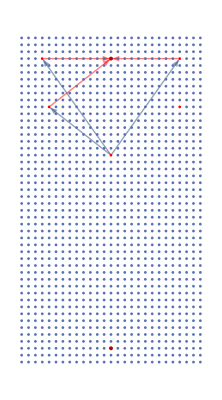

```mathematica
vertices = Table[{i, j}, {i, 1, courtWidth, 2}, {j, 1, courtLength, 2}];
toHighlight ={hoopHome, hoopAway};
fullCourt = Graph[Flatten[vertices, 1],Join[passes, shotsStyled], VertexCoordinates->Flatten[vertices, 1], GraphHighlight->toHighlight, VertexSize->Large,  VertexStyle->Map[#->Red&, homePlayers]]
```

Assessing the quality of a position

```mathematica
numAttackVectors = Length[shots];
```

Okay so finally what I have here is a single metric for how spread out the players are. What I do is simply take the log of the differences of all the x coordinates, then do the same with y, then sum it all up. I tried using variance, std,mad initially, but the issue was that all three gave too much weight to large variations for my liking. In the game, it is better to have all your players spread out a little bit then one player spread out a lot. So I needed to weight the large variations lower. This is the reason  for the log. The one issue with this method was that if the differences were 0 the log gives -oo so if it is 0 I just set the value to 0 and don’t take the log to work around this. Here is a manipulate to play around with player positions and see how it affects the metric. It looks good to me so far.

```mathematica
Manipulate[Module[{players,diffsX, diffsY, logDifferencesX, logDifferencesY, playersWithin1Pass, playersInShotRange, threatPlayers, passes, shots, shotsStyled, fullCourt, toEnlarge, spreadFactor, numAttackVectors},
players = {pt1,pt2, pt3, pt4, pt5};
playersWithin1Pass= getPointsWithinDistance[ball,players, maxPassLength];
playersInShotRange = getPointsWithinDistance[hoopAway,players, maxShotLength];
threatPlayers =Intersection[playersWithin1Pass, playersInShotRange]; 
passes = getEdges[ball, threatPlayers];
shots = getEdgesAll[threatPlayers, hoopAway];
shotsStyled = Style[#, Red]&/@ shots;
toEnlarge = #->1&/@ players;
fullCourt = Graph[
Flatten[vertices, 1],
Join[passes, shotsStyled], 
VertexCoordinates->Flatten[vertices, 1],GraphHighlight->toHighlight,  VertexSize->toEnlarge
 ];
diffsX = Differences[players[[All, 1]]];
diffsY = Differences[players[[All, 2]]];logDifferencesX=If[#==0,Floor[#],Log[Abs[#]]]&/@diffsX;logDifferencesY=If[#==0,Floor[#],Log[Abs[#]]]&/@diffsY;
spreadFactor = N@Total[{Total[logDifferencesX], Total[logDifferencesY]}];
numAttackVectors = Length[shots];
Column[{fullCourt, spreadFactor, numAttackVectors}]
],
Row[
{Control[{pt1,{1, 1}, { 54, 95}, {2,2}}], 
Control[{pt2,{1, 1}, { 54, 95}, {2,2}}], 
Control[{pt3,{1, 1}, { 54, 95}, {2, 2}}], 
Control[{pt4,{1, 1}, { 54, 95}, {2, 2}}], 
Control[{pt5,{1, 1}, { 54, 95}, {2, 2}}]}]]
```

The next step is to have the manipulate show the graph. First what I need is to have the sliders have jumps of 2 instead of 1.

It’s too slow when I edit directly in the graph, I’m going to set the variables here and then run the graph after

```mathematica
{
Slider2D[Dynamic[pt1], {{1, 1}, {54, 95}, {2,2}}, ImageSize->{54*3, 94*3}], Dynamic[pt1], 
Slider2D[Dynamic[pt2], {{1, 1}, {54, 95}, {2,2}}, ImageSize->{54*3, 94*3}], Dynamic[pt2],
Slider2D[Dynamic[pt3], {{1, 1}, {54, 95}, {2,2}}, ImageSize->{54*3, 94*3}], Dynamic[pt3],
Slider2D[Dynamic[pt4], {{1, 1}, {54, 95}, {2,2}}, ImageSize->{54*3, 94*3}], Dynamic[pt4],
Slider2D[Dynamic[pt5], {{1, 1}, {54, 95}, {2,2}}, ImageSize->{54*3, 94*3}], Dynamic[pt5]
}
```

{,,,,,,,,,}

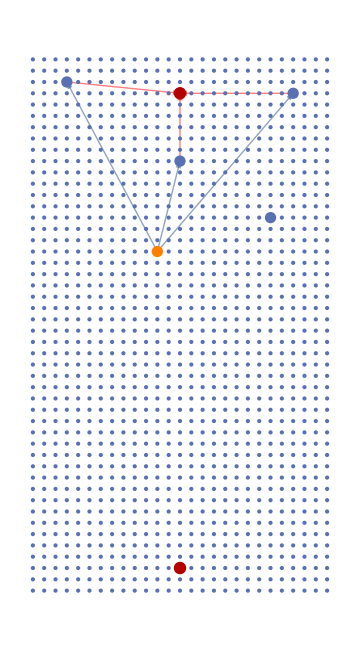
-Graphics-
19.8795
3

StringJoin::string: String expected at position 2 in node [ 
id List[27, 5]
graphics [
fill "#828FA3"
outline "#000000"
x 27
y 5
w 1
h 1
]
<>System`Convert`GraphletDump`WriteAttribute[GraphHighlight,True]<>VertexSize "1"
].

Riffle::list: List expected at position 1 in Riffle[System`Convert`GraphletDump`IndentString[node [ 
id List[27, 5]
graphics [
fill "#828FA3"
outline "#000000"
x 27
y 5
w 1
h 1
]
<>System`Convert`GraphletDump`WriteAttribute[GraphHighlight,True]<>VertexSize "1"
]],
	].

StringJoin::string: String expected at position 1 in StringJoin[Riffle[System`Convert`GraphletDump`IndentString[node [ 
id List[27, 5]
graphics [
fill "#828FA3"
outline "#000000"
x 27
y 5
w 1
h 1
]
<>System`Convert`GraphletDump`WriteAttribute[GraphHighlight,True]<>VertexSize "1"
]],
	]].

StringJoin::string: String expected at position 2 in node [ 
id List[27, 89]
graphics [
fill "#828FA3"
outline "#000000"
x 27
y 89
w 1
h 1
]
<>System`Convert`GraphletDump`WriteAttribute[GraphHighlight,True]<>VertexSize "1"
].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Riffle::list: List expected at position 1 in Riffle[System`Convert`GraphletDump`IndentString[node [ 
id List[27, 89]
graphics [
fill "#828FA3"
outline "#000000"
x 27
y 89
w 1
h 1
]
<>System`Convert`GraphletDump`WriteAttribute[GraphHighlight,True]<>VertexSize "1"
]],
	].

```mathematica
players = {pt1, pt2, pt3, pt4, pt5};
possessorOfBall = pt1;
playersWithin1Pass= getPointsWithinDistance[possessorOfBall,players, maxPassLength];
playersInShotRange = getPointsWithinDistance[hoopAway,players, maxShotLength];
threatPlayers =If[MemberQ[playersInShotRange, possessorOfBall], Append[Intersection[playersWithin1Pass, playersInShotRange],possessorOfBall], Intersection[playersWithin1Pass, playersInShotRange]];
passes = getEdges[possessorOfBall, threatPlayers];
shots = getEdgesAll[threatPlayers, hoopAway];
shotsStyled = Style[#, Red]&/@ shots;
toEnlarge = Join[#->1&/@ Join[players, hoops]];
diffsX = Differences[players[[All, 1]]];
diffsY = Differences[players[[All, 2]]];logDifferencesX=If[#==0,Floor[#],Log[Abs[#]]]&/@diffsX;logDifferencesY=If[#==0,Floor[#],Log[Abs[#]]]&/@diffsY;
spreadFactor = N@Total[{Total[logDifferencesX], Total[logDifferencesY]}];
numAttackVectors = Length[shots];
Column[{fullCourt = Graph[
Flatten[vertices, 1],
Join[passes, shotsStyled], 
VertexCoordinates->Flatten[vertices, 1],GraphHighlight->toHighlight,  VertexSize->toEnlarge, ImageSize->Medium, VertexStyle->{possessorOfBall->Orange}
 ],
spreadFactor,
numAttackVectors}
]
```

Okay so above we have a a way to visualize and evaluate the quality of a position in basketball

The next step is to evaluate not just the snap shot of the position but start to incorporate how the position can morph into other positions. Let’s allow for dribbling within a certain radius and then make the pass and shot edges  be dashed and dribbling be dotted I guess I’ll see

Idea: What games would not lead to caring about the middle. Well baseball. Any goal sports. List of goal sports: basketball, football, soccer, chess, hockey, etc. This gives you optionality which gives you control. Another idea is to have

Another idea is the preference for bottom up rules. In the NBA they’re tending to not have plays. In soccer they don’t have plays. Why this process as opposed to a top down mechanism?

Okay first I want to show the number of places you can go as you change the location.

Let’s state the laws and see if the model captures those laws

### Law #1: The middle is advantageous proportional to the speed of the ball

Up to the limit of the court size

and maybe inversely proportional to the ratio of the shot range to the size of the court but I have to think about how the importance of the middle is impacted by shot range and court size

```mathematica
{Slider2D[Dynamic[pt1], {{1, 1}, {53, 95}, {2,2}}, ImageSize->{54*3, 94*3}],Dynamic[pt1], Slider[Dynamic[speedOfBall], {1, 30}], Dynamic[speedOfBall]}
```

{,,,}

```mathematica
(*shotRange= getPointsWithinDistance[hoopAway, Flatten[vertices, 1], *)
passablePoints  = getPointsWithinDistance[pt1, Flatten[vertices, 1], speedOfBall];
passableEdges = getEdges[pt1, passablePoints];
regularVertexSizes = #->0.5&/@Flatten[vertices, 1];
toEnlarge = #->1&/@ Join[hoops, {pt1}];
Graph[
Flatten[vertices, 1],
passableEdges, 
VertexCoordinates->Flatten[vertices, 1],GraphHighlight->toHighlight,  ImageSize->Medium, VertexSize->Join[regularVertexSizes, toEnlarge]
]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[vertices,1].

Flatten::flev: The level argument 1→0.5 in position 2 of Flatten[vertices→0.5,1→0.5] should be a non-negative integer or Infinity giving the levels to flatten through or a list of lists of levels to flatten together.

Rule::argrx: Rule called with 4 arguments; 2 arguments are expected.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[vertices,1].

Join::heads: Heads Flatten and Rule at positions 1 and 2 are expected to be the same.

Graph[Flatten[vertices,1],getEdges[{39,39},getPointsWithinDistance[{39,39},Flatten[vertices,1],1.]],VertexCoordinates→Flatten[vertices,1],GraphHighlight→toHighlight,ImageSize→Medium,VertexSize→Join[Flatten[vertices→0.5,1→0.5],Rule[hoops,1,{{39,39}},1]]]

In games where kids aren’t able to throw long passes and the speed of the ball is really slow, it doesn’t actually help to get the ball to the middle that much because they can’t take advantage of it with long passes

### Law #2: The dispersion of players is directly proportional to the speed of the ball

One constraint on this is it only works when the ball moves faster than the player. Otherwise there is no advantage to passing over dribbling

You see this in kids soccer where because they don’t have the ability to pass the ball quickly and accurately, there is no advantage to spreading out

Let’s forget about the hoops for a second. The reason it makes sense to do this is because its about getting the ball in dangerous positions. The way to do that is to maximize the number of points you can access and therefore maximize the number of paths to the basket and the variance of those paths. It seems like to me there are two reasons for why variance is advantageous. One is you minimize overlap and another reason is you maximize the variance of your attack vectors

Let’s add one player. Where should we put him. Any point where the distance to the original point is equal to the speed of the ball

#### Adding one player

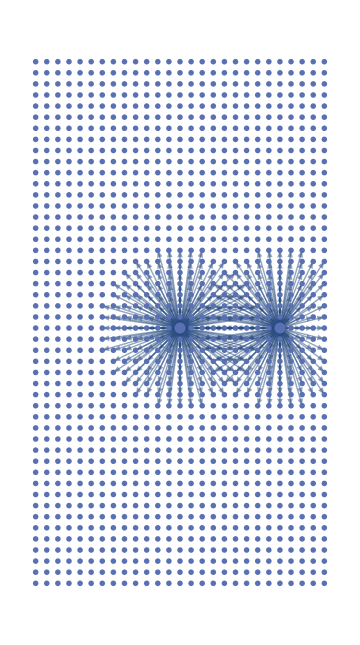
{-Graphics-,277}

```mathematica
passablePoints  = getPointsWithinDistance[pt1, Flatten[vertices, 1], speedOfBall];
passableEdges = getEdges[pt1, passablePoints];
regularVertexSizes = #->0.5&/@Flatten[vertices, 1];
passablePointspt2 = getPointsWithinDistance[pt2,Flatten[vertices, 1], speedOfBall];
passableEdgespt2 = getEdges[pt2, passablePointspt2];
toEnlarge = {pt1->1, pt2->1};
{Graph[
Flatten[vertices, 1],
Join[passableEdges, passableEdgespt2], 
VertexCoordinates->Flatten[vertices, 1],ImageSize->Medium, VertexSize->Join[regularVertexSizes, toEnlarge]
], Length[Union[Join[passablePoints, passablePointspt2]]]}
```

The court coverage is measured by the number of points reached:

507

```mathematica
{Slider2D[Dynamic[pt1], {{1, 1}, {53, 95}, {2,2}}, ImageSize->{54*3, 94*3}],Dynamic[pt1],Slider2D[Dynamic[pt2], {{1, 1}, {53, 95}, {2,2}}, ImageSize->{54*3, 94*3}],Dynamic[pt2], Slider[Dynamic[speedOfBall], {1, 30, 1}], Dynamic[speedOfBall]}
```

{,,,,,}

```mathematica
potentialPoints =
```

#### Adding 5 players

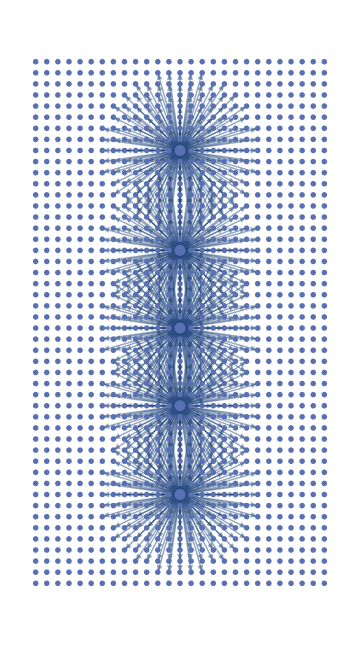
{-Graphics-,618}

```mathematica
players = {pt1, pt2, pt3, pt4, pt5};
passablePointsList  = getPointsWithinDistance[#, Flatten[vertices, 1], speedOfBall]&/@ players;
passableEdgesList = MapThread[getEdges[#1, #2]&, {players, passablePointsList}];
regularVertexSizes = #->0.5&/@Flatten[vertices, 1];
toEnlarge = #->1&/@ players;
{Graph[
Flatten[vertices, 1],
Flatten[passableEdgesList, 1], 
VertexCoordinates->Flatten[vertices, 1],ImageSize->Medium, VertexSize->Join[regularVertexSizes, toEnlarge]
], Length[Union[Flatten[passablePointsList, 1]]]}
```

The court coverage is measured by the number of points reached:

507

```mathematica
Grid[{{Slider2D[Dynamic[pt1], {{1, 1}, {53, 95}, {2,2}}, ImageSize->{54*3, 94*3}],Dynamic[pt1],Slider2D[Dynamic[pt2], {{1, 1}, {53, 95}, {2,2}}, ImageSize->{54*3, 94*3}],Dynamic[pt2], 
Slider2D[Dynamic[pt3], {{1, 1}, {53, 95}, {2,2}}, ImageSize->{54*3, 94*3}],Dynamic[pt3]}, 
{Slider2D[Dynamic[pt4], {{1, 1}, {53, 95}, {2,2}}, ImageSize->{54*3, 94*3}],Dynamic[pt4], 
Slider2D[Dynamic[pt5], {{1, 1}, {53, 95}, {2,2}}, ImageSize->{54*3, 94*3}],Dynamic[pt5], 
Slider[Dynamic[speedOfBall], {1, 30, 1}], Dynamic[speedOfBall]}}]
```

|  |  |  |  | 
 |  |  |  |  |

Okay so what’s bugging me about the above model is that you would never want to line up your players like that. I thought about it for a while and the reason is that you care more about the space near the ball then the space away from the ball. But I don’t want to add complexity to the mode. This model captures two of my initial ideas, first being that the middle is more valuable then the edges and the second is that players tend to spread out.

## Circular Passing Microstructure

### Core functionality

#### Neutral graphics

```mathematica
ballPoint = {0,0}
maxPassLength = 20
maxPassRing = Circle[ballPoint, maxPassLength]
neutralGraphics = {neutralColor, PointSize[0.05],Point[ballPoint], maxPassRing}
```

{0,0}

20

Circle[{0,0},20]

{RGBColor[0.39542229343099106, 0.2037842374303807, 0.006607156481269551],PointSize[0.05],Point[{0,0}],Circle[{0,0},20]}

#### Defensive graphics

This is proportional to the speed of the defender:

```mathematica
defenderArcAngles= {{Pi/8,3Pi/8}, {5Pi/8,7Pi/8}}
```

{{π/8,(3 π)/8},{(5 π)/8,(7 π)/8}}

```mathematica
defenderArcs= Circle[ballPoint,maxPassLength, #]&/@defenderArcAngles
defensiveGraphics= Join[{defensiveColor,  Thickness[0.025],Opacity[0.3]}, defenderArcs]
```

{Circle[{0,0},20,{π/8,(3 π)/8}],Circle[{0,0},20,{(5 π)/8,(7 π)/8}]}

{RGBColor[0.7877775234607461, 0.01850919356069276, 0.018326085297932403],Thickness[0.025],Opacity[0.3],Circle[{0,0},20,{π/8,(3 π)/8}],Circle[{0,0},20,{(5 π)/8,(7 π)/8}]}

#### Offensive graphics

```mathematica
attackerPoints ={{-20, 15}, {-5, 16},{19, 19}} 
offensiveGraphics = {offensiveColor,PointSize[0.05], Point/@ attackerPoints}
```

{{-20,15},{-5,16},{19,19}}

{RGBColor[0.30214389257648583, 0.5284962233920806, 0.010528725108720532],PointSize[0.05],{Point[{-20,15}],Point[{-5,16}],Point[{19,19}]}}

#### Visualization

Now let’s graph all these objects

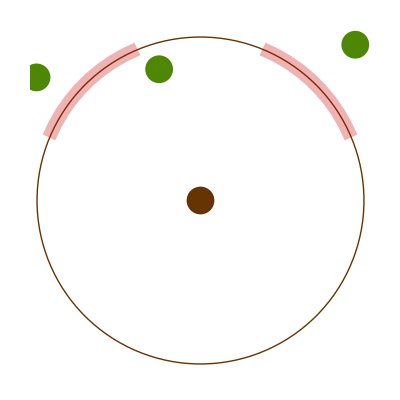

```mathematica
Graphics[{neutralGraphics, defensiveGraphics, offensiveGraphics} ]
```

## 1d Model Implementation

### Initializing Stationary Pass Model

```mathematica
idIdxs = <|{"Ball", 1}->{1, 1},{"Passer", 1}->{2, 1}, {"Attacker", 1}->{2, 6}, {"Defender", 1}->{2, 11}|>;
courtSize = 10;
ballSpeed = 2;
playerSpeed = 1;
reactionTime = 1;
colorRules = {1->Orange, 2->Black, 3->Blue, 4->Red};
playerAgility = 1;
{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}
```

```mathematica
CellObject["ceb8ec24-bc0e-43e2-b61e-42f28d7f0470","53f1d203-8fd3-42da-8861-83bbadecb8a5"]
```

### Functions Stationary Pass Model

#### Low level functions

```mathematica
incrementObjectIdx[{i_, j_}, direction_]:= {i, j+direction}
getIdxFromPosition[{type_, position_}]:=If[type == "Ball", {1, position}, {2, position}]
setPosition[{type_, id_}, position_]:= idIdxs[{type, id}] = getIdxFromPosition[{type, position}]
getIdx[{type_, id_}]:= idIdxs[{type, id}]
getPosition[{type_, id_}]:= idIdxs[{type, id}][[2]]
getObjectStationaryIdxList[idx_, nSteps_]:= Table[idx, nSteps]
```

#### Mid level Functions

```mathematica
getObjectMovementIdxs[startIdx_, endIdx_]:= Module[{distance, direction},
distance = endIdx[[2]]  - startIdx[[2]];
direction = If[Positive[distance], 1, -1];
NestList[incrementObjectIdx[#, direction] &,startIdx, Abs[distance]]
]
getObjectNStepIdxs[{type_, id_}, endPosition_, nSteps_, delay_:0]:=
  Module[{movementIdxs, movementIdxsDelayed, nStepsArray},
movementIdxs = getObjectMovementIdxs[getIdx[{type, id}], getIdxFromPosition[type, endPosition]];
movementIdxsDelayed =Join[Table[First[movementIdxs], delay],movementIdxs];
nStepsArray = PadRight[movementIdxsDelayed, nSteps, {Last[movementIdxsDelayed]}]
]
```

Likely will change this:

```mathematica
getGameFrame[{ballIdx_, passerIdx_, attackerIdx_, defenderIdx_}]:=
ReplacePart[emptyGameArray, {ballIdx->1, passerIdx->2, attackerIdx->3, defenderIdx->4}]
```

```mathematica
showGame[gameArray_]:=ArrayPlot[gameArray, Mesh->True, ColorRules->colorRules]
```

#### High level functions

```mathematica
getPassIdxs[ball_, passer_, attacker_, defender_]:= Module[{ballPosition, attackerPosition,nSteps, allObjectMovements},
ballPosition = getPosition[ball]; attackerPosition = getPosition[attacker];
nSteps = Abs[attackerPosition - ballPosition]+1;
allObjectMovements = {
getObjectNStepIdxs[ball, attackerPosition, nSteps],
getObjectStationaryIdxList[getIdx[passer],nSteps],
getObjectStationaryIdxList[getIdx[attacker],nSteps],
getObjectNStepIdxs[defender, attackerPosition, nSteps, reactionTime]
};
Transpose[allObjectMovements]
]
```

Algorithm if pass is open:

```mathematica
OpenQ[ball_, attacker_, defender_]:=
(getPosition[defender] - getPosition[attacker] + reactionTime) / playerSpeed > (getPosition[attacker] - getPosition[ball]) / ballSpeed
```

### Testing Stationary Pass Model

```mathematica
ball = {"Ball", 1};
passer = {"Passer", 1};
attacker = {"Attacker", 1};
defender =  {"Defender", 1};
```

```mathematica
setPosition[ball, 1];
setPosition[passer, 1];
setPosition[attacker, 5];
setPosition[defender, 10];
```

```mathematica
OpenQ[ball, attacker, defender]
```

False

```mathematica
allObjectFrameIdxs = getPassIdxs[ball, passer, attacker, defender];
gameFrames = Map[getGameFrame, allObjectFrameIdxs];
movementPlots = Map[showGame, gameFrames];
ListAnimate[movementPlots]
```

### Player Movement Model

#### Legacy Functions

```mathematica
getPotentialBallStates[{ballCurrentPosition_,ballDestinationPosition_ }]:=Module[{potentialDestinations},
potentialDestinations = If[ballDestinationPosition == 1, NestWhileList[#+ballSpeed&,ballCurrentPosition, #<=courtSize-ballSpeed&], {ballDestinationPosition}];
{getPotentialBallPosition[ballCurrentPosition, #],#}& /@ potentialDestinations
]
getPotentialBallStatesSmart[{ballState_,attackerState_, defenderState_ }]:=Module[{potentialDestinations},
{getPotentialBallPosition[ballState[[1]], #],#}& /@ getPotentialThrowPositionsSmart[{ballState, attackerState, defenderState}]
]
getPotentialThrowPositionsSmart[{ballState_, attackerState_, defenderState_}]:=
Module[{legalThrowDestinations, smartThrowDestinations},
legalThrowDestinations = NestWhileList[#+ballSpeed&,ballState[[2]], #<=courtSize-ballSpeed&];
smartThrowDestinations = DeleteCases[legalThrowDestinations, destination_/;playerCanReachQ[attackerState, destination,(destination - ballStartPosition)/ballSpeed]  &&
(!playerCanReachQ[defenderState, destination,(destination - ballStartPosition)/ballSpeed])]
]
playerCanReachQ[playerState_, destination_, nSteps_] := 
Module[{distance, agilityDelay},
distance = destination - playerState[[1]];
agilityDelay = If[Sign[distance] != Sign[playerState[[2]]], playerAgility, 0]; 
(Abs[distance]+agilityDelay)/ playerSpeed <= nSteps
]
openLongQ[{attackerState_, defenderState_}]:=attackerState[[1]]>defenderState[[1]]&& attacker[[1]]<=maxOpenLongPosition
getPotentialPlayerStates[{position_, velocity_}]:= Module[{forwardQ, backwardQ, allPossibleMoves},
forwardQ = position<=(courtSize - playerSpeed)&& NonNegative[velocity];
backwardQ = position> (playerSpeed)&&NonPositive[velocity];
allPossibleMoves = {{position - playerSpeed, -playerSpeed}, {position, 0}, {position+playerSpeed, playerSpeed}};
Replace[{backwardQ, forwardQ}, 
{{True, True}->allPossibleMoves, 
{True, False}->allPossibleMoves[[;;2]], 
{False, True}->allPossibleMoves[[2;;]], 
{False, False}->{allPossibleMoves[[2]]}}]
]
getPotentialPlayerStatesSmart[{playerState_, ballState_}]:= Module[{forwardQ, backwardQ, allPossibleMoves},
If[ballInAirQ[ballState], catch[ballState], 
forwardQ = playerState[[1]]<=(courtSize - playerSpeed)&& NonNegative[velocity];
backwardQ = playerState[[1]]> (playerSpeed)&&NonPositive[velocity];
allPossibleMoves = {{playerState[[1]] - playerSpeed, -playerSpeed}, {playerState[[1]], 0}, {playerState[[1]]+playerSpeed, playerSpeed}};
Replace[{backwardQ, forwardQ}, 
{{True, True}->allPossibleMoves, 
{True, False}->allPossibleMoves[[;;2]], 
{False, True}->allPossibleMoves[[2;;]], 
{False, False}->{allPossibleMoves[[2]]}}]
]]
getPotentialAttackerStates[{ballState_, attackerState_, defenderState_}]:=
Which[
openLongQ[{attackerState, defenderState}], {attackerState+playerSpeed}, 
True, getPotentialPlayerStatesSmart[{attackerState, ballState}]
]
ballInAirQ[ballState_]:=ballState[[1]]!=ballState[[2]]

caughtPassQ[{ballState_, attackerState_, defenderState_}]:=
ballState[[1]]!=1&&
ballState[[1]] == ballState[[2]] && 
attackerState[[1]] ==ballState[[1]]&& 
defenderState[[1]]!=attackerState[[1]] 

incompletePassQ[{ballState_, attackerState_, defenderState_}]:=
ballState[[1]]!=1 && ballState[[1]] == ballState[[2]]&& (attackerState[[1]] != ballState[[1]] || attackerState[[1]]== defenderState[[1]])
getGameResult[{ballState_, attackerState_, defenderState_, nSteps_, turn_}]:=
Module[{objectPositions = Join[ballState, {attackerState[[1]], defenderState[[1]]}]},
Which[
caughtPassQ[objectPositions], 1,
incompletePassQ[objectPositions], -1,
nSteps>=gameLength, -1
]
]

getPotentialStates[{ballState_,attackerState_, defenderState_, nSteps_, turn_}]:=
Module[{objectPositions= Join[ballState,{attackerState[[1]], defenderState[[1]]}]},
Which[
nSteps>=gameLength, {},
SameQ[turn , α], If[caughtPassQ[objectPositions]||incompletePassQ[objectPositions], {},Tuples[{getPotentialBallStates[ballState], getPotentialPlayerStates[attackerState],{defenderState},{nSteps},{β} }]],
SameQ[turn , β], Tuples[{getPotentialBallStates[ballState], {attackerState},getPotentialPlayerStates[defenderState],{nSteps+1},{α} }]
]]
showGame[{ballState_, attackerState_,defenderState_, nSteps_, turn_}]:=
ArrayPlot[
ReplacePart[emptyGameArray, {{1, ballState[[1]]}->1, {2, attackerState[[1]]}->2, {2, defenderState[[1]]}->3} ],
Mesh->True, ColorRules->{1->Orange, 2->Blue, 3->Red}]
showGameSim[{ballState_, attackerState_,defenderState_, nSteps_}]:=
ArrayPlot[
ReplacePart[emptyGameArray, {{1, ballState[[1]]}->1, {2, attackerState[[1]]}->2, {2, defenderState[[1]]}->3} ],
Mesh->True, ColorRules->{1->Orange, 2->Blue, 3->Red}]
turnQ[gameState_]:=Last[gameState]
vertexShapeFunction = (Inset[showGame[#2],#1,Center,30#3]&);
```

#### New Functions

```mathematica
getPotentialBallPosition[currentPosition_,destination_]:=
If[destination>currentPosition,currentPosition+ballSpeed, currentPosition]
getPotentialBallStatesSmart[{ballState_,attackerState_, defenderState_ }]:=Module[{potentialDestinations},
Map[{getPotentialBallPosition[ballState[[1]], #],#}& ,getPotentialThrowPositionsSmart[{ballState, attackerState, defenderState}]]
]
catch[playerState_, ballDestination_]:=If[ballDestination == playerState[[1]],{playerState[[1]]},If[ballDestination > playerState[[1]] , {playerState[[1]]+playerSpeed},{playerState[[1]]- playerSpeed} ]]

getPotentialThrowPositionsSmart[{ballState_, attackerState_, defenderState_}]:=
Module[{legalThrowDestinations, attackerCanReach, defenderCantReach},
If[ballState[[2]] !=1, {ballState[[2]]},
If[openLongQ[{attackerState, defenderState}],If[attackerState[[1]] == maxOpenLongPosition, {maxThrowPosition},{ballStartPosition}], 
legalThrowDestinations = NestWhileList[#+ballSpeed&,ballState[[2]], #<=courtSize-ballSpeed&];
attackerCanReach = DeleteCases[legalThrowDestinations, destination_/;!playerCanReachQ[attackerState, destination,(destination - ballStartPosition)/ballSpeed]];
defenderCantReach = DeleteCases[legalThrowDestinations,destination_/; playerCanReachQ[defenderState, destination,(destination - ballStartPosition)/ballSpeed]];
Union[{ballStartPosition}, Intersection[attackerCanReach, defenderCantReach]]
]]]

playerCanReachQ[playerState_, destination_, nSteps_] := 
Module[{distance, agilityDelay},
distance = destination - playerState[[1]];
agilityDelay = If[playerState[[2]]!=0,If[Sign[distance] != Sign[playerState[[2]]], playerAgility, 0], 0];
(Abs[distance]+agilityDelay)/ playerSpeed <= nSteps
]
openLongQ[{attackerState_, defenderState_}]:=attackerState[[1]]>defenderState[[1]]&& attacker[[1]]<=maxOpenLongPosition

getPotentialPlayerStatesSmart[{playerState_, ballState_}]:= Module[{forwardQ, backwardQ,stationaryQ,legalMoves, allPossibleMoves},
If[ballInAirQ[ballState], catch[playerState, ballState[[2]]], 
backwardQ = playerState[[1]]>= (minDistanceToPasser - ballStartPosition)+ballSpeed&&NonPositive[playerState[[2]]];
(*Players need to move more*)
stationaryQ = playerState[[2]] != 0;
forwardQ = playerState[[1]]<=(courtSize - playerSpeed)&& NonNegative[playerState[[2]]];
allPossibleMoves = {{playerState[[1]] - playerSpeed, -playerSpeed}, {playerState[[1]], 0}, {playerState[[1]]+playerSpeed, playerSpeed}};
legalMoves = Flatten@Position[{backwardQ, stationaryQ, forwardQ}, True];
allPossibleMoves[[legalMoves]]
]]

getPotentialAttackerStates[{ballState_, attackerState_, defenderState_}]:=
Which[
openLongQ[{attackerState, defenderState}], {{attackerState[[1]]+playerSpeed, playerSpeed}}, 
True, getPotentialPlayerStatesSmart[{attackerState, ballState}]
]
ballInAirQ[ballState_]:=ballState[[1]]!=ballState[[2]]

getPotentialStatesSimultaneous[{ballState_,attackerState_, defenderState_, nSteps_}]:=
Module[{objectStates= {ballState, attackerState, defenderState}},
Which[
nSteps>=gameLength, {},
caughtPassQ[objectStates]||incompletePassQ[objectStates], {},
True, 
Tuples[
{getPotentialBallStatesSmart[objectStates],getPotentialAttackerStates[objectStates],
getPotentialPlayerStatesSmart[{defenderState, ballState}],{nSteps+1}}]]
]
shadowPlayer[{ballState_, attackerState_, defenderState_}]:=
If[ballInAirQ[ballState], catch[ballState]]
```

#### Initializing

Each player is a vector i.e. the first part is the position and the second part is the velocity
Note: The ball has two parts the first is currentPosition the second is destinationPosition, the reason for this is so that you can look at one frame and tell if it is a caught pass or not

```mathematica
courtSize = 10;
ballSpeed = 2;
playerSpeed = 1;
reactionTime = 1;
colorRules = {1->Orange, 2->Black, 3->Blue, 4->Red};
playerAgility = 1;
emptyGameArray = ConstantArray[0, {2, courtSize}]
```

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

1

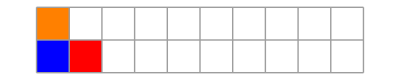

```mathematica
gameLength = 4;
ballStartPosition  = 1
ball = {ballStartPosition, 1}; attacker = {1,0}; defender = {2, 0}; nSteps = 0; turn = α;
initialGameState = {ball, attacker, defender, nSteps, turn};
showGame[initialGameState]
```

Stats to use for functions

```mathematica
maxThrowPosition = courtSize  - Mod[ballStartPosition, ballSpeed];
maxThrowDistance = maxThrowPosition - ballStartPosition;
timeMaxThrow = maxThrowDistance / ballSpeed;
maxOpenLongPosition = playerSpeed(maxThrowPosition - timeMaxThrow);
```

#### Initializing Simulataneous and Smart Version

```mathematica
gameLength = 10;
ballStartPosition  = 1;
ball = {ballStartPosition, 1}; attacker = {1,0}; defender = {2, 0}; nSteps = 0;
objectStates = {ball, attacker, defender}
initialGameState = {ball, attacker, defender, nSteps};
showGameSim[initialGameState]
```

{{1,1},{1,0},{2,0}}

-Graphics-

#### Testing Simultaneous function

```mathematica
getPotentialStatesSimultaneous[b]
```

{{{1,1},{2,0},{3,0},2},{{1,1},{2,0},{4,1},2},{{1,1},{3,1},{3,0},2},{{1,1},{3,1},{4,1},2}}

```mathematica
Tuples[{{},{a, b}, {1, 2} }]
```

{}

```mathematica
b = %[[2]]
```

{{1,1},{2,1},{3,1},1}

{}

```mathematica
b
```

{{1,1},{2,1},{3,1},1}

```mathematica
getPotentialPlayerStatesSmart[{{3, 1}, {1, 1}}]
```

{{3,0},{4,1}}

```mathematica
showGameSim/@ getPotentialStatesSimultaneous[%[[2]]]
```

{}

```mathematica
b = VertexList[ng]
```

getPotentialStates[getPotentialStates[{{1,1},{1,0},{2,0},0}]]

```mathematica
If[ballInAirQ[{1, 9}], catch[{4, 0}, 9]]
```

{5}

#### Alpha beta search graph

TODO: Make module to fix this

```mathematica
alphaBetaGraph = Graph[EdgeList[VertexReplace[ResourceFunction["AlphaBetaSearch"][getPotentialStates, initialGameState,turnQ, getGameResult],x_:>Annotation[showGame[x],x]] ],GraphLayout->"LayeredDigraphEmbedding",AspectRatio->1/2,VertexLabels->Placed["Name",Tooltip],EdgeStyle->Arrowheads[.01], PerformanceGoal->"Quality",ImageSize->Large, VertexSize->0.5]
```

```mathematica
alphaBetaHighlighted = HighlightGraph[ResourceFunction["FixedPointGraph"][
getPotentialStates,{initialGameState},GraphLayout->"LayeredDigraphEmbedding",
EdgeStyle->Lighter@Gray,AspectRatio->2/3], {Style[alphaBetaGraph,Lighter@Orange]}]
```

#### Nest Graph

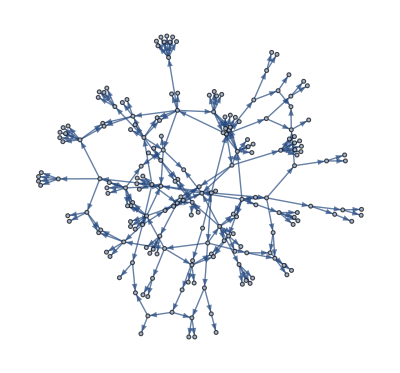

```mathematica
ng = NestGraph[getPotentialStatesSimultaneous, {initialGameState}, 5]
```

```mathematica
Graph[EdgeList[VertexReplace[ng,x_:>Annotation[showGameSim[x],x]] ],GraphLayout->"LayeredDigraphEmbedding",AspectRatio->1/2,VertexLabels->Placed["Name",Tooltip],EdgeStyle->Arrowheads[.01], PerformanceGoal->"Quality",ImageSize->Large, VertexSize->2]
```

-Graphics-

graph where equal board states at different times are merged

```mathematica
Graph[EdgeList[VertexReplace[ng,x_:>showGameSim[x]]],GraphLayout->"LayeredDigraphEmbedding",AspectRatio->1/2,VertexLabels->Placed["Name",Tooltip],EdgeStyle->Arrowheads[.01], PerformanceGoal->"Quality",ImageSize->Large, VertexSize->0.5]
```

-Graphics-

#### Let’s first actually try without a defender because there are so many possibilities

Let’s assume these object starting points

```mathematica
objects = {
ball = {"Ball", 1},
passer = {"Passer", 1},
attacker = {"Attacker", 1},
defender = {"Defender", 1}
};
setPosition[ball, 1];
setPosition[passer, 11];
setPosition[attacker, 1];
setPosition[defender, 11];
currentIdxs = getIdx/@ objects
```

{{1,1},{2,11},{2,1},{2,11}}

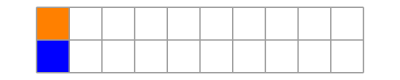

```mathematica
showGame[getGameFrame[currentIdxs]]
```

```mathematica
ballRow =getGameFrame[currentIdxs][[1]]
playerRow=getGameFrame[currentIdxs][[2]];
```

{1,0,0,0,0,0,0,0,0,0}

```mathematica
getAllPossibleNextStates[{ballRow_, playerRow_}]:=
Tuples[{{SequenceReplace[ballRow, {{1, 0, 0} :> Sequence[0, 0, 1]}], ballRow}, 
DeleteDuplicates[{SequenceReplace[playerRow, {{3, 0} :> Sequence[0, 3]}], playerRow, SequenceReplace[playerRow, {{0,3} :> Sequence[3,0]}]}]}]
```

#### NestGraph Without Defender

{ball, attacker, defender, NStepsGoneBy}

```mathematica
{ballPosition,attackerPosition,defenderPosition,nSteps}
```

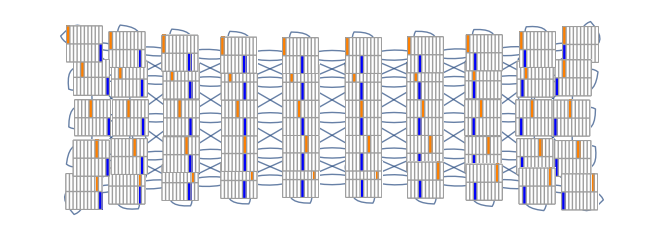

```mathematica
g =NestGraph[getAllPossibleNextStates, {{ballRow, playerRow}}, 10, VertexShapeFunction->(Inset[showGame[#2],#1,Center,13#3]&)]
```

#### Alpha beta search example

```mathematica
gnim=ResourceFunction["AlphaBetaSearch"][Function[state,Thread[{Catenate[Map[Tuples[MapAt[Range[0,First[#]-1]&,Map[List,First[state]],#]]&,Range[Length[First[state]]]]],<|α->β,β->α|>[Last[state]]}]],{{1,2,3},α},Last[#]&,Association[α->-1,β->1][Last[#]]&]
```

```mathematica
Function[state,Thread[{Catenate[Map[Tuples[MapAt[Range[0,First[#]-1]&,Map[List,First[state]],#]]&,Range[Length[First[state]]]]],<|α->β,β->α|>[Last[state]]}]][{{1, 2, 3},α} ]
```

{{{0,2,3},β},{{1,0,3},β},{{1,1,3},β},{{1,2,0},β},{{1,2,1},β},{{1,2,2},β}}

### Optimal Defender Behavior

### Alternative General Movement Using Rules

```mathematica
SequenceReplace[{0, 0, 0, 3, 2, 0, 0}, {{0, 3} :> Sequence[3, 0],{_,2} :> Sequence[2, 0]}]
```

{0,0,3,0,2,0,0}

### Passing

```mathematica
throwBall1Step[ballIdx]:= ballIdx[[1]]+

getObjectRules[objectIdxs_List]:= 
 Join[
{objectIdxs[[1]]->Orange, objectIdxs[[2]]->Black}, If[objectIdxs[[3]] == objectIdxs[[4]], {objectIdxs[[3]]->Purple, objectIdxs[[4]]->Purple},{objectIdxs[[3]]->Blue, objectIdxs[[4]]->Red}]
]
getGameArray[objectRules_] := ReplacePart[emptyGameArray, objectRules]
```

```mathematica
passSteps = 5;
passArray = NestList[throwBall1Step, objectIdxs, passSteps];
objectRulesList = getObjectRules/@ passArray;
gameArrayList = Map[getGameArray, objectRulesList, {1}]
```

{getGameArray[getObjectRules[objectIdxs]],getGameArray[getObjectRules[throwBall1Step[objectIdxs]]],getGameArray[getObjectRules[throwBall1Step[throwBall1Step[objectIdxs]]]],getGameArray[getObjectRules[throwBall1Step[throwBall1Step[throwBall1Step[objectIdxs]]]]],getGameArray[getObjectRules[throwBall1Step[throwBall1Step[throwBall1Step[throwBall1Step[objectIdxs]]]]]],getGameArray[getObjectRules[throwBall1Step[throwBall1Step[throwBall1Step[throwBall1Step[throwBall1Step[objectIdxs]]]]]]]}

```mathematica
passAnimation = ListAnimate[ArrayPlot[#, Mesh->True]&/@ gameArrayList]
```

ArrayPlot::mat: Argument getGameArray[getObjectRules[objectIdxs]] at position 1 is not a list of lists.

ArrayPlot::mat: Argument getGameArray[getObjectRules[throwBall1Step[objectIdxs]]] at position 1 is not a list of lists.

ArrayPlot::mat: Argument getGameArray[getObjectRules[throwBall1Step[throwBall1Step[objectIdxs]]]] at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

### Defender Movement

```mathematica
moveDefender1Step[objectIdxs_List, direction_Integer:-1]:=Module[{defenderIdx},
defenderIdx =objectIdxs[[4]];
ReplacePart[objectIdxs, 4->{defenderIdx[[1]], defenderIdx[[2]]+(playerSpeed*direction)}]]
```

```mathematica
moveSteps = 5
defenderMoveArray = NestList[moveDefender1Step, objectIdxs, moveSteps]
objectRulesList = getObjectRules/@ defenderMoveArray;
gameArrayList = Map[getGameArray, objectRulesList, {1}]
```

5

{objectIdxs,moveDefender1Step[objectIdxs],moveDefender1Step[moveDefender1Step[objectIdxs]],moveDefender1Step[moveDefender1Step[moveDefender1Step[objectIdxs]]],moveDefender1Step[moveDefender1Step[moveDefender1Step[moveDefender1Step[objectIdxs]]]],moveDefender1Step[moveDefender1Step[moveDefender1Step[moveDefender1Step[moveDefender1Step[objectIdxs]]]]]}

{getGameArray[getObjectRules[objectIdxs]],getGameArray[getObjectRules[moveDefender1Step[objectIdxs]]],getGameArray[getObjectRules[moveDefender1Step[moveDefender1Step[objectIdxs]]]],getGameArray[getObjectRules[moveDefender1Step[moveDefender1Step[moveDefender1Step[objectIdxs]]]]],getGameArray[getObjectRules[moveDefender1Step[moveDefender1Step[moveDefender1Step[moveDefender1Step[objectIdxs]]]]]],getGameArray[getObjectRules[moveDefender1Step[moveDefender1Step[moveDefender1Step[moveDefender1Step[moveDefender1Step[objectIdxs]]]]]]]}

```mathematica
moveAnimation = ListAnimate[ArrayPlot[#, Mesh->True]&/@ gameArrayList]
```

ArrayPlot::mat: Argument getGameArray[getObjectRules[objectIdxs]] at position 1 is not a list of lists.

ArrayPlot::mat: Argument getGameArray[getObjectRules[moveDefender1Step[objectIdxs]]] at position 1 is not a list of lists.

ArrayPlot::mat: Argument getGameArray[getObjectRules[moveDefender1Step[moveDefender1Step[objectIdxs]]]] at position 1 is not a list of lists.

General::stop: Further output of ArrayPlot::mat will be suppressed during this calculation.

## 1D Model With Time on the Y-Axis

#### Functions

```mathematica
getPotentialTimeStampsBall[position_]:=Module[{minTime},
minTime = (position - ballStartPosition) / ballSpeed;
Range[minTime, gameLength]
]
stitchTimeStamps[position_, timeStamps_]:={#, position}&/@ timeStamps
getBallDestinationTimePair[]:=
Module[{legalThrowDestinations, distances},
legalThrowDestinations = Rest[NestWhileList[#+ballSpeed&,ballStartPosition, #<=courtSize-ballSpeed&]];stitchTimeStamps[#, getPotentialTimeStampsBall[#]]&/@ legalThrowDestinations
]
showGameTimeY[{ballState_, attackerState_,defenderState_, nSteps_}]:= 
ArrayPlot[
ReplacePart[emptyFullPlayArray,Flatten[getBallDestinationTimePair[], 1]->5],
Mesh->True, ColorRules->{1->Orange, 2->Blue, 3->Red, 5->Green}]
```

```mathematica
getPotentialPlayerStatesAtTime[{{position_, velocity_}, nStep_}]:= Module[{forwardQ, backwardQ, allPossibleMoves},
forwardQ = (minDistanceToPasser - ballStartPosition)+ballSpeed&&NonPositive[playerState[[2]]];

backwardQ = position> (playerSpeed)&&NonPositive[velocity];
allPossibleMoves = {{position - playerSpeed, -playerSpeed}, {position, 0}, {position+playerSpeed, playerSpeed}};
Replace[{backwardQ, forwardQ}, 
{{True, True}->({#, nStep+1}&/@allPossibleMoves), 
{True, False}->({#, nStep+1}&/@allPossibleMoves[[;;2]]), 
{False, True}->({#, nStep+1}&/@allPossibleMoves[[2;;]]), 
{False, False}->({#, nStep+1}&/@{allPossibleMoves[[2]]})}]
]
```

```mathematica
getTimeArrayIdx[{{position_, velocity_}, nStep_}]:={position, gameLength - nStep+1}

getPlayerTree[startPosition_]:=NestGraph[getPotentialPlayerStatesAtTime, {{startPosition, 0}, 1}, gameLength - 1]

getVertexValuesMean[currentValues_]:=Mean/@ Join[{currentValues[[;;2]]}, Partition[currentValues, 3, 1], {currentValues[[-2;;]]}]

getIdxEdge[edge_]:=DirectedEdge[{edge[[1,1, 1]], gameLength - edge[[1, 2]]+1}, {edge[[2, 1, 1]], gameLength - edge[[2, 2]]+1}]

getPassEdges[passVertexList_]:= #[[1]]->#[[2]]&/@Partition[passVertexList, 2, 1]

getNextPassVertex[currentVertex_]:={currentVertex[[1]]+2, currentVertex[[2]] - 1}

getPathValue[g_, s_, t_]:=If[FindPath[g, s, t] == {}, 0, t[[1]]]

getDefenderGraph [defenderState_]:= Module[{defenderTree, defenderCoords},
defenderTree= NestGraph[getPotentialPlayerStatesAtTime, {defenderState}, gameLength - nSteps];defenderCoords = getTimeArrayIdx/@VertexList[defenderTree];Graph[defenderTree, VertexCoordinates->defenderCoords]
]
```

```mathematica
getVertexValue[passGraph_, defenderGraph_]:=Module[{passLocationsCovered},
passLocationsCovered  = Intersection[GraphEmbedding@defenderGraph, getPassLocations[passGraph]];
Total[passLocationsCovered[[All, 1]]]
]
```

```mathematica
getPassList[row_]:=
NestWhileList[getNextPassVertex, {1, row}, (#[[1]]<courtSize - ballStartPosition) && #[[2]]>1&]
```

```mathematica
getPassLocations[passGraph_]:=Module[{edges, edgeVertices},
edges = EdgeList[passGraph];
edgeVertices = Join[edges[[All, 1]], edges[[All, 2]]];
Select[edgeVertices, #[[1]]>=5&]
]
passStyle[edges_]:=Style[#, Dashed, Thick, successColor]&/@ edges

defenderStyle[edges_]:=Style[#, defensiveColor]&/@ edges
```

```mathematica
getPassGraph[]:=Module[{vertices, passThrowRows, passLists, passEdges, styledEdges,passLocations},
vertices = Flatten[Table[{i, j}, {i, 1, courtSize,1}, {j, 1, gameLength, 1}], 1];
passThrowRows  = Range[gameLength - 1, 2, -1];
passLists = getPassList/@ passThrowRows;
passLocations = Select[Flatten[passLists, 1], #[[1]]>=5&];
passEdges = Flatten@Map[getPassEdges, passLists, {1}];
styledEdges = Style[#, Dashed]&/@ passEdges;
Graph[vertices,styledEdges, VertexCoordinates->vertices, VertexStyle->(#->Green&/@passLocations), VertexSize->0.25]
]
```

```mathematica
getPassGraphWithDefender[passGraph_, defenderState_]:= Module[{defenderGraph, defenderEdges, passVerticesStyled},
defenderGraph = getDefenderGraph[defenderState];
defenderEdges = defenderStyle@Union[getIdxEdge/@ EdgeList[defenderGraph]];
passVerticesStyled = #->successColor&/@getPassLocations[passGraph];
Graph[VertexList[passGraph],Join[passStyle[EdgeList[passGraph]],defenderEdges], VertexCoordinates->VertexList[passGraph], VertexStyle->Join[{getTimeArrayIdx[defenderState]->defensiveColor},passVerticesStyled], VertexSize->0.25]
]
```

#### Initializing

Each player is a vector i.e. the first part is the position and the second part is the velocity
Note: The ball has two parts the first is currentPosition the second is destinationPosition, the reason for this is so that you can look at one frame and tell if it is a caught pass or not

```mathematica
courtSize = 20;
ballSpeed = 2;
playerSpeed = 1;
reactionTime = 1;
colorRules = {1->Orange, 2->Black, 3->Blue, 4->Red};
playerAgility = 1;
gameLength = 10;
ballStartPosition  = 1;
ball = {ballStartPosition, 1}; attacker = {1,0}; defender = {2, 0}; nSteps = 0; turn = α;
initialGameState = {ball, attacker, defender, nSteps};
emptyFullPlayArray = ConstantArray[0, {gameLength, courtSize}];
minDistanceToPasser = 3;
```

Stats to use for functions

```mathematica
maxThrowPosition = courtSize  - Mod[ballStartPosition, ballSpeed];
maxThrowDistance = maxThrowPosition - ballStartPosition;
timeMaxThrow = maxThrowDistance / ballSpeed;
maxOpenLongPosition = playerSpeed(maxThrowPosition - timeMaxThrow);
```

#### Ball Pass Tree

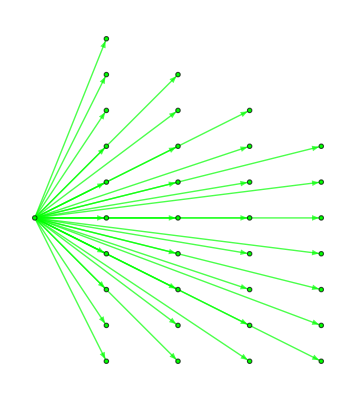

```mathematica
head = {1, Floor[courtSize/2]};
leaves ={#[[2]], courtSize - #[[1]]+1}&/@ Flatten[getBallDestinationTimePair[], 1];
vertices = Prepend[leaves, head];
branches = head->#&/@ leaves;
passGraph = Graph[vertices, branches, VertexCoordinates->vertices, VertexStyle->Green, EdgeStyle->Green]
```

#### Player Movement Tree

```mathematica
playerTree= NestGraph[getPotentialPlayerStatesAtTime, {{{1, 0}, 1}}, gameLength - 1];
```

```mathematica
playerCoordinates = getTimeArrayIdx/@VertexList[playerTree];
```

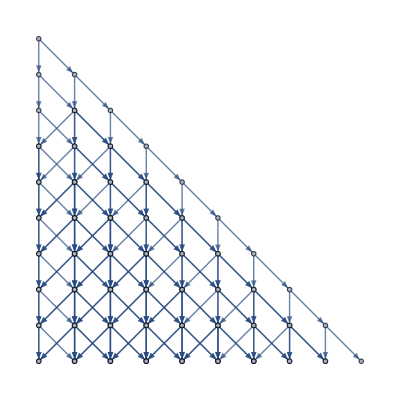

```mathematica
Graph[playerTree, VertexCoordinates->playerCoordinates]
```

#### Optimal Start Position Calculation

```mathematica
vertexValues = Reverse@(N/@NestList[getVertexValues, start, 5]);
```

```mathematica
MatrixForm[vertexValues]
```

(2.27662 | 2.51775 | 3. | 3.48225 | 3.72338
2.13194 | 2.4213 | 3. | 3.5787 | 3.86806
1.95833 | 2.30556 | 3. | 3.69444 | 4.04167
1.75 | 2.16667 | 3. | 3.83333 | 4.25
1.5 | 2. | 3. | 4. | 4.5
1. | 2. | 3. | 4. | 5.)

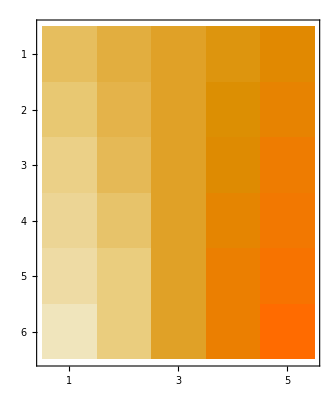

```mathematica
MatrixPlot[vertexValues]
```

#### Optimal Defending

Create a 10 by 5 graph

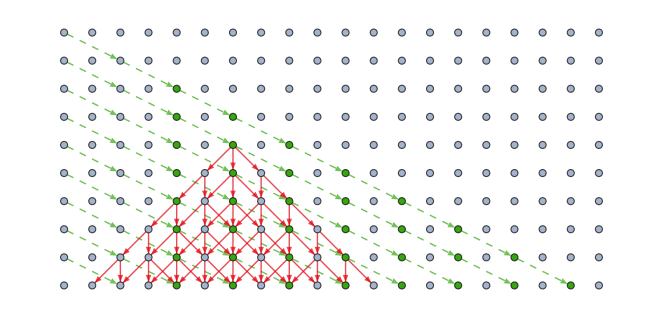

```mathematica
nSteps = 5;
defenderInitialPosition = 7;
defenderInitialState = {{defenderInitialPosition, 0}, nSteps};
defenderStates = {{#, 0}, nSteps}&/@ Range[minDistanceToPasser+ ballStartPosition, courtSize];
passGraph =getPassGraph[];
defenderGraph = getDefenderGraph[defenderInitialState];
passGraphsWithDefender = getPassGraphWithDefender[passGraph, defenderInitialState]
```

```mathematica
defenderGraphs = getDefenderGraph/@ defenderStates;
```

```mathematica
getVertexValue[passGraph, #]&/@ defenderGraphs
```

{348,348,348,348,348,348,348,348,348,348,348,348,348,348,348,348,348}

```mathematica
getVertexValue[passGraph, #]&/@ defenderGraphs
```

{135,168,192,220,230,242,237,225,213,201,180,164,148,128,108,97,73}

```mathematica
optimalDistance1DModel[row_, passGraph_, defenderGraph_]:=Module[{defenderGraphs},
defenderGraphs = 
PositionLargest[getVertexValue[passGraph, #]&/@ defenderGraphs][[1]]
```

This is not right^

## 2D Model

### Trying to model 1v1 dribbling, too hard will come back

Seems too hard will come back to it

```mathematica
offensePositions = {{0, 0}};
defensivePositions = {{0, 5}};

playerSize = 1;
playerSpeed = 1;
offensiveDisks = Map[Disk[#, playerSize]&, offensePositions];
defensiveDisks = Map[Disk[#, playerSize]&, defensivePositions];
halfcourt=Rectangle[{-50,0},{50,100}];
Graphics[{White, halfcourt, defensiveColor,defensiveDisks,offensiveColor,offensiveDisks}]
time = 5;
```

-Graphics-

### John 2D Idea

```mathematica
Manipulate[
Module[{halfcourt,passerposition,defenderpositions,defenderZOC,passerZOC,ballspeed},
ballspeed=passvelocity;
passerposition={26,0};
halfcourt=Rectangle[{0,0},{52,47}];
passerZOC=Disk[passerposition,1];
SeedRandom[1234];
defenderpositions=RandomPoint[halfcourt,5];
defenderZOC=Map[Disk[#,EuclideanDistance[#,passerposition]/ballspeed]&,defenderpositions];
Graphics[{LightBlue,halfcourt,LightRed,defenderZOC,Darker@Green,passerZOC}]
],{{passvelocity,10},1,10},ControlPlacement->Top,SaveDefinitions->True,TrackedSymbols:>passvelocity]
```

### Backdoor pass 2D

TODO: Make defender ring accurate, my idea is to use distance from passer. Right now it uses the time when the ball passes the defender

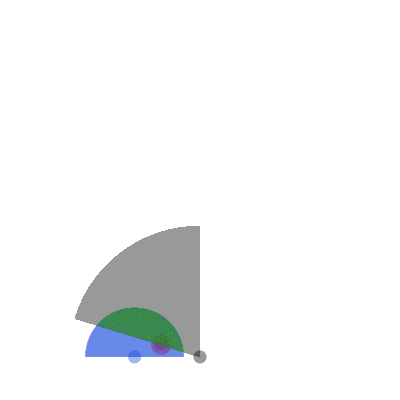

```mathematica
Module[{passerPosition, attackerPositions, defenderPositions,playerSize, offenseSpeed, defenseSpeed, ballSpeed, reactionTime, maxPassDecisionTime, maxBallInAirTime, attackerDisks, perpindicularPassLine, intersectionPoint, interceptionWindow, defenderDisks, defenseRangeDisk, passLine, passRangeDisk, attackerRangeDisk, passerToDefenderAngle, passerDisk, halfcourt, passArea, discreteRegion, discretePassArea},

passerPosition= {0, 1};attackerPositions = {{-10, 1}};defenderPositions = {{-6, 3}};playerSize = 1;
offenseSpeed = 1.5;defenseSpeed = 1;ballSpeed = 4;reactionTime = 1;maxPassDecisionTime = 2;
maxBallInAirTime = 3;halfcourt=Rectangle[{-25,0},{25,50}];
passerDisk = Disk[passerPosition, playerSize];
attackerDisks = Map[Disk[#, playerSize]&, attackerPositions];
defenderDisks = Map[Disk[#, playerSize]&, defenderPositions];
perpindicularPassLine = Round/@Line[{defenderPositions[[1]], AngleVector[defenderPositions[[1]],{20, Pi/4}]}];
intersectionPoint = ResourceFunction["LineIntersection"][passLine, perpindicularPassLine];
interceptionWindow = EuclideanDistance[passerPosition, intersectionPoint]/ballSpeed ;
defenseRangeDisk = Disk[defenderPositions[[1]], EuclideanDistance[defenderPositions[[1]], passerPosition]*defenseSpeed /ballSpeed];
passLine  = Round/@Line[{passerPosition, AngleVector[passerPosition,{ballSpeed*(maxPassDecisionTime+maxBallInAirTime),3Pi/4}]}];
passerToDefenderAngle = Pi -VectorAngle[{defenderPositions[[1, 1]], 1}, defenderPositions[[1]]];
passRangeDisk = Disk[passerPosition, ballSpeed*(maxPassDecisionTime+maxBallInAirTime) , {Pi/2, passerToDefenderAngle}];
attackerRangeDisk = Disk[attackerPositions[[1]], offenseSpeed*(maxPassDecisionTime+maxBallInAirTime), {Pi, 0}];
passArea = BooleanRegion[#1&&#2&,{passRangeDisk,Disk[{-10,1},7.5]}];
discretePassArea=DiscretizeRegion[passArea];
Graphics[{White, halfcourt, defenderColor,Opacity[0.4],defenderDisks,attackerColor,attackerDisks,attackerRangeDisk, neutralColor, passerDisk,defenderColor,defenseRangeDisk,  neutralColor, passRangeDisk, attackerColor, Opacity[0.4], attackerRangeDisk, successColor,Opacity[0.4],MeshPrimitives[discretePassArea,2]}]
]
```

### Discrete 2D Graphics Module

#### Functions

```mathematica
getPoint[center_,angle_,radius_]:=center+radius*AngleVector[angle]
edgeToLine[edge_]:= Line[{edge[[1]], edge[[2]]}]
getAwayPoints[homePoints_, homeAwayDistance_:1/10]:= Map[{#[[1]],#[[2]] + homeAwayDistance}&, homePoints]

getHexRow[startPoint_, rowLength_]:= NestList[getPoint[#, 60Degree, 1]&, startPoint, rowLength];

getHomePoints[length_]:=Module[{hexRowLengths,startPoint, hexStartPointsLeft, hexStartPointsBottom, startPoints, allPoints},
	hexRowLengths = Join[Range[length, 2length], Range[2length - 1, length, -1]];
	startPoint = {0, 0};
	hexStartPointsLeft = NestList[getPoint[#, -60Degree, 1]&, startPoint, length];
	hexStartPointsBottom = NestList[getPoint[#, 0Degree, 1]&, getPoint[Last@hexStartPointsLeft, 0Degree, 1], length - 1];
	startPoints= Join[hexStartPointsLeft, hexStartPointsBottom];
	allPoints = Flatten[MapThread[getHexRow[#1, #2]&, {startPoints, hexRowLengths}], 1]
]

getRecPoints[point_, size_]:={getPoint[point, 225Degree, size], getPoint[point, 45Degree, size]}
getTriPoints[point_, size_]:=
{getPoint[point, 88Degree, size - 1/12],getPoint[point, 210 Degree, size], getPoint[point, 330Degree, size ]}

getBallLocation[team_,possessor_]:= Module[{shape},
	shape=  
	If[team == "home", 
	Rectangle@@getRecPoints[homePlayers[[possessor]], playerSize],
	Polygon[getTriPoints[awayPlayers[[possessor]], playerSize]]];
	RegionCentroid[shape]
]
```

```mathematica
Options[showGame] = {highlightPoints->{}};
showGame[{homePlayers_, awayPlayers_ , ballLoc_, turn_, guardedCount_}, OptionsPattern[{showPlay, showGame}]]:=Module[{hpRecs, apTris, allShapes, dribbler,ball},
	hpRecs = Rectangle@@getRecPoints[#, playerSize]&/@ homePlayers;
	apTris = N/@Polygon@getTriPoints[#,playerSize]&/@ awayPlayers;
	ball = Disk[ballLoc, ballSize];
	Graphics[{FaceForm@White,background, FaceForm@Gray, Point@N@OptionValue[points], FaceForm@Blue, hpRecs,FaceForm@Red,apTris, Green, ball,
	Purple, Point@OptionValue[highlightPoints]}]
]
getPlayerLoc[team_, i_]:= If[team == "home", homePlayers[[i]], awayPlayers[[i]]]

getMovesBounded[currentPoint_, speed_:1]:=Module[{allPoints},
  allPoints = Map[getPoint[currentPoint, #, speed]&, directions];
  Select[allPoints, RegionMember[gamePoly, #]&]
]

getMovesBoundedStatic[currentPoint_, speed_:1]:=Module[{allPoints},
  allPoints = Append[Map[getPoint[currentPoint, #, speed]&, directions], currentPoint];
  Select[allPoints, RegionMember[gamePoly, #]&]
]

getObjectMovementFrames[start_, end_, frames_:20]:= Subdivide[start, end,frames]

showMove[gameStateStart_, gameStateEnd_, frameRate_:20]:= Module[{graphicsFrames}, 
  graphicsFrames = getMoveFrameGraphics[gameStateStart, gameStateEnd, frameRate];
  ListAnimate[graphicsFrames, DefaultDuration->1, AnimationRepetitions->1]
 ]

getMoveFrames[gameStateStart_, gameStateEnd_, frameRate_:10]:= Module[{go1, go2, gf1, gf2, turn, gc, hpl, apl, objectFrames, gameStatesFlat, 
gameObjectFrames, gameStates}, 
  go1 = gameStateStart[[;;2]];
  go2 = gameStateEnd[[;;2]];
  gf1 = Append[Flatten[go1, 1], gameStateStart[[3]]];
  gf2 = Append[Flatten[go2,1], gameStateEnd[[3]]];
  turn = gameStateEnd[[4]]; gc = gameStateEnd[[5]];
  objectFrames = MapThread[getObjectMovementFrames[#1, #2, frameRate]&, {gf1, gf2}];
  gameStatesFlat = Transpose[objectFrames];
  hpl = Length@homePlayers; apl = Length@awayPlayers;
  gameObjectFrames = {#[[;;hpl]], #[[hpl+1;;hpl+apl]],#[[hpl+apl+1]]}&/@ gameStatesFlat;
  gameStates = Join[#, {turn, gc}]& /@ gameObjectFrames
  ]

getMoveFrameGraphics[gameStateStart_, gameStateEnd_, frameRate_:10]:= Module[{moveFrames}, 
  moveFrames = getMoveFrames[gameStateStart, gameStateEnd, frameRate];
  showGame/@ moveFrames
  ]
```

```mathematica
guardedQ[{homePlayers_, awayPlayers_ , ballLoc_, turn_, guardedCount_}]:=
    MemberQ[awayPlayers, {ballLoc[[1]], ballLoc[[2]]+1/10}] || MemberQ[homePlayers, {ballLoc[[1]], ballLoc[[2]]-1/10}]

flip[turn_]:= Replace[turn, {"α"->"β","β"->"α"}]

  possessionQ[players_, ballLoc_]:= MemberQ[players, ballLoc]
  possession[{homePlayers_, awayPlayers_ , ballLoc_, turn_}] := 
    Which[
	MemberQ[homePlayers, ballLoc], "α",
	MemberQ[awayPlayers, ballLoc], "β",
	True, "α"]
```

```mathematica
getBestGames[{objects__, turn_, guardedCount_}, n_:5]:= Module[{lgs, sorter},
lgs = getLegalGames[{objects, turn, guardedCount}];
sorter = If[turn == "α", TakeLargestBy, TakeSmallestBy];
sorter[lgs, evaluateState, UpTo[n]]
]

getRandomBestGame[{objects__, turn_, guardedCount_}, n_:5]:= Module[{lgs, sorter},
lgs = getLegalGames[{objects, turn, guardedCount}];
sorter = If[turn == "α", TakeLargestBy, TakeSmallestBy];
RandomChoice@sorter[lgs, evaluateState, UpTo[n]]
]

turnover[{homePlayers_, awayPlayers_ , {ballX_, ballY_}, turn_, guardedCount_}]:= 
Module[{maySteal, awayStealY, homeStealY, awaySteal, homeSteal},
maySteal = guardedCount == stealDifficulty;
awayStealY = ballY+homeAwayDistance;
homeStealY =  ballY-homeAwayDistance;
awaySteal = MemberQ[awayPlayers, {ballX,awayStealY}];
homeSteal =MemberQ[homePlayers, {ballX,homeStealY}];
Which[
maySteal&&awaySteal,  {homePlayers, awayPlayers, {ballX, awayStealY}, "β", -1},
maySteal&&homeSteal,  {homePlayers, awayPlayers, {ballX, homeStealY}, "α", -1},
awaySteal||homeSteal,  {homePlayers, awayPlayers, {ballX, ballY}, turn, guardedCount+1},
True, {homePlayers, awayPlayers , {ballX, ballY}, turn, 0}
]]
```

```mathematica
mergeGames[attackerGameState_,defenderGameState_]:=  
{attackerGameState[[1]], defenderGameState[[2]], attackerGameState[[3]], attackerGameState[[4]], defenderGameState[[5]]}

getCorners[team_]:= Module[{locs},
locs= If[team == "home", homeLocs, awayLocs];
{getPoint[locs[[topLeftIdx]], 180Degree, 1], 
getPoint[locs[[topLeftIdx]], 0Degree, courtLength+1],
 getPoint[locs[[bottomRightIdx]], 180Degree, courtLength+1], 
getPoint[locs[[bottomRightIdx]], 0Degree, 1]}
]

getBallMoves[ballLoc_, turn_]:= Module[{allPoints},
  If[turn == "α", Select[homeLocs, EuclideanDistance[ballLoc, #]<= ballSpeed &], 
  Select[awayLocs, EuclideanDistance[ballLoc, #]<= ballSpeed &]]
]
```

```mathematica
Options[showPlay] = {points->{}};
showPlay[moves_, op___]:= Module[{}, 
attackingTeam =moves[[1, 4]]; defendingTeam = flip@attackingTeam;
delay = 5;
movePairs = Partition[moves, 2, 1];
attackingMovePairs  = Select[movePairs, #[[2, 4]] == defendingTeam&];
defendingMovePairs = Select[movePairs, #[[2, 4]] == attackingTeam&];
attackingFrames =  Flatten[getMoveFrames@@@ attackingMovePairs, 1];
defendingFrames = Flatten[getMoveFrames@@@ defendingMovePairs, 1];
allFrames =alignFrames[attackingFrames, defendingFrames];
mergedFrames = MapThread[mergeGames[#1, #2]&, allFrames];
graphics = showGame[#, op]& /@ mergedFrames;
ListAnimate[graphics, DefaultDuration->5, AnimationRepetitions->1]
]
```

```mathematica
alignFrames[attackers_, defenders_]:=Module[{},
defendersDelayed = Join[Table[First@defenders, delay], defenders];
lengthDiff = Length@attackers - Length@defendersDelayed;
Which[
lengthDiff == 0, {attackers, defendersDelayed},
Positive[lengthDiff], {attackers, Join[defendersDelayed, Table[Last@defendersDelayed, lengthDiff]]},
Negative[lengthDiff], {Join[attackers, Table[Last@attackers, -1*lengthDiff]], defendersDelayed}
]]
```

```mathematica
mergeGames[attackerGameState_,defenderGameState_]:=  
{attackerGameState[[1]], defenderGameState[[2]], attackerGameState[[3]], attackerGameState[[4]], defenderGameState[[5]]}
```

```mathematica
evaluateState[{homePlayers_, awayPlayers_ , ballLoc_, turn_, guardedCount_}]:=Module[{players, oppPlayers},
  {players, oppPlayers}=  If[turn == "α", {homePlayers, awayPlayers},{awayPlayers, homePlayers}];
	Which[
	(*td*)
	MemberQ[homePlayers,ballLoc]&&ballLoc[[2]] == homeEndZoneY, 100,
	MemberQ[awayPlayers,ballLoc]&&ballLoc[[2]] == awayEndZoneY, -100,
	MemberQ[homePlayers,ballLoc], ballLoc[[2]] - awayEndZoneY+2/10,
	MemberQ[awayPlayers,ballLoc], ballLoc[[2]] - homeEndZoneY+ 1/10,
	True, 0]
	]
```

```mathematica
turnoverQ[{homePlayers_, awayPlayers_ , {ballX_, ballY_}, turn_, guardedCount_}]:= 
Module[{maySteal, awaySteal, homeSteal},
maySteal = guardedCount == stealDifficulty;
awaySteal = MemberQ[awayPlayers, {ballX,ballY + homeAwayDistance}];
homeSteal =MemberQ[homePlayers, {ballX,ballY - homeAwayDistance}];
If[(maySteal && awaySteal) || (maySteal && homeSteal), True, False]
]
```

```mathematica
Options[getLegalGames] = {overlaps->False, incompletePasses->False,travels->True, shorten->True, duplicatesBy->"ball"};
 getLegalGames[{homePlayers_, awayPlayers_ , ballLoc_, turn_, guardedCount_}, op___]:= Module[{},
{players, oppPlayers}=  If[turn == "α", {homePlayers, awayPlayers},{awayPlayers, homePlayers}] ;
pos = MemberQ[players, ballLoc];
pg = If[pos, FirstPosition[players, ballLoc][[1]], Missing[]];
ballLocs = If[pos, getBallMoves[ballLoc, turn],{ballLoc}];
playerMoves = getPlayerMoves[players, pos, pg];
allMoves = Append[playerMoves, ballLocs];
allMoveComs = getLegal[Tuples[allMoves], pos, ballLoc, pg, op];
ballMoved =  allMoveComs[[All,-1]];
playersMoved =  allMoveComs[[All,;;Length@players]];
gameStates = If[turn == "α", 
MapThread[{#1, oppPlayers, #2, "β", guardedCount}&, {playersMoved, ballMoved}],
MapThread[{oppPlayers,#1, #2, "α", guardedCount}&, {playersMoved, ballMoved}]
];
gameStatesWithTOs = turnover/@ gameStates
]
```

```mathematica
getAttackerGameState[move_, {homePlayers_, awayPlayers_ , ballLoc_, turn_, guardedCount_} ]:=Module[{},
replaceFunc = If[turn == "α",{Most[#], awayPlayers, Last[#], "β", guardedCount}&,{homePlayers, Most[#],Last[#], "α", guardedCount}&];
replaceFunc[move]
]
```

```mathematica
getDefenderGameState[move_, {homePlayers_, awayPlayers_ , ballLoc_, turn_, guardedCount_} ]:=Module[{},
replaceIdx = If[turn == "α", 1, 2];
ReplacePart[{homePlayers, awayPlayers , ballLoc, flip@turn, guardedCount}, replaceIdx->move]
]
```

```mathematica
showAttackingMove[{players__, ballLoc_}, team_, OptionsPattern[{showPlay, showGame}]]:=Module[{hpRecs, apTris, allShapes, dribbler},
playerShapes = If[team == "home",  Rectangle@@getRecPoints[#, playerSize]&/@ {players}, 
 N@Polygon@getTriPoints[#,playerSize]&/@ awayPlayers];
ball = Disk[ballLoc, ballSize];
color = If[team== "home", Blue, Red];
Graphics[{FaceForm@White,background, FaceForm@Gray, Point@N@OptionValue[points], FaceForm@color, playerShapes, Green, ball,
	Red, Point@OptionValue[highlightPoints]}]]
```

```mathematica
Options[getBestMove] = {overlaps->False, incompletePasses->False,travels->True, shorten->True, duplicatesBy->"ball"};
getBestMove[{homePlayers_, awayPlayers_ , ballLoc_, turn_, guardedCount_}, op___]:=  Module[{},
{players, oppPlayers}=  If[turn == "α", {homePlayers, awayPlayers},{awayPlayers, homePlayers}] ;
{attackingTeam, attackerTurn} = If[MemberQ[homePlayers, ballLoc], {"home", "α"},{"away", "β"}] ;
pos = MemberQ[players, ballLoc];
{attackers, defenders} = If[pos, {players, oppPlayers}, {oppPlayers, players}];
currentGameState = {homePlayers, awayPlayers , ballLoc, turn, guardedCount};
pg = FirstPosition[attackers, ballLoc][[1]];
amoves = getAttackerMoves[attackers,ballLoc, attackerTurn, pg];
amovesFiltered = filterMoves[amoves,True, ballLoc, pg, op];
bestAttackingMoves=  TakeLargestBy[amovesFiltered, evaluateAttackingState[#,defenders, attackingTeam]&, UpTo[5]];
If[pos, getAttackerGameState[RandomChoice@bestAttackingMoves,currentGameState],
bestDefensiveMoves = getBestDefensiveMoves[defenders, bestAttackingMoves[[All, 3]], 3]; 
getDefenderGameState[RandomChoice@bestDefensiveMoves, currentGameState]
]]
```

```mathematica
showDefensiveMove[players_, team_, OptionsPattern[{showPlay, showGame}]]:=Module[{hpRecs, apTris, allShapes, dribbler},
playerShapes = If[team == "home",  Rectangle@@getRecPoints[#, playerSize]&/@ players, 
 N/@Polygon@getTriPoints[#,playerSize]&/@ players];
color = If[team== "home", Blue, Red];
Graphics[{FaceForm@White,background, FaceForm@Gray, Point@N@OptionValue[points], FaceForm@color, playerShapes,
	Red, Point@OptionValue[highlightPoints]}]]
```

```mathematica
evaluateAttackingState[move_, defenders_, attackingTeam_:"home"]:=Module[{},
ballLoc = Last[move];
attackers = Most[move];
d =If[attackingTeam == "home", 1, -1];
had  = homeAwayDistance*d;
iq = interceptionQ[ballLoc, defenders, had];
ez = If[attackingTeam == "home", homeEndZoneY, awayEndZoneY];
Which[
iq,(ballLoc[[2]] - homeEndZoneY+had),
	(*td*)
	MemberQ[attackers,ballLoc]&&ballLoc[[2]] == homeEndZoneY, 100,
MemberQ[attackers,ballLoc], ballLoc[[2]] - awayEndZoneY+2/10,
	True, 0]
	]
```

```mathematica
interceptionQ[{ballX_, ballY_}, defenderLocs_, had_]:=Module[{},
MemberQ[defenderLocs, {ballX,ballY + had}]
]
```

```mathematica
evaluateDefensiveState[defense_, ballLocs_] := Module[{},
ballDistances = getDistancesToBall[defense, #]&/@ ballLocs;
sumMinDistances = Total[Min/@ ballDistances]
]
```

```mathematica
overlayAttackingMove[gameState_, move_]:= showGame[ReplacePart[gameState, {1->Most[move], 3->Last[move]}] ]
```

```mathematica
overlayDefendingMove[gameState_, move_, op__]:= showGame[ReplacePart[gameState, 2->move], op]
```

```mathematica
getAttackerMoves[players_,ballLoc_, turn_, pg_, rule_:"static"]:=Module[{},
playerMoves = If[rule == "static",getMovesBoundedExcept[players, pg],getMovesBounded/@ players];
ballMoves= getBallMoves[ballLoc, turn];
allMoves = Append[playerMoves, ballMoves];
Tuples[allMoves]
]
```

```mathematica
filterMoves[moveComs_, pos_:False, ballLoc_:Nothing, pg_:Nothing, OptionsPattern[getBestMove]]:= Module[{},
(*If duplicates by is ball it only takes one instance of each ball location otherwise 
it removes all cases where players are in same formation*)
dupsBy = If[pos && OptionValue[duplicatesBy] == "ball", Last, Sort];
filters = {DeleteDuplicatesBy[#, dupsBy]&};
If[!OptionValue[overlaps], AppendTo[filters, removeOverlaps]];
If[pos && !OptionValue[incompletePasses], AppendTo[filters, removeIncompletePasses]];
If[pos && OptionValue[travels], AppendTo[filters, removeTravelling[#, ballLoc, pg]&]];
(Composition@@filters)[moveComs]
]
```

```mathematica
getBestDefensiveMoves[defenders_, ballLocs_, n_:1]:= Module[{},
defenderPositionsList = filterMoves@getDefenderMoves[defenders];
bestPos = TakeSmallestBy[defenderPositionsList, evaluateDefensiveState[#, ballLocs]&, n]
]
```

```mathematica
getDefenderMoves[currentLocs_]:=Tuples[(getMovesBounded/@ currentLocs)]
```

```mathematica
getMovesBoundedExcept[players_, pg_]:=  Insert[(getMovesBounded/@Delete[players, pg]), {players[[pg]]}, pg]
```

```mathematica
getDistancesToBall[players_, ball_]:= EuclideanDistance[#, ball]&/@ players
```

```mathematica
removeOverlaps[moveComs_]:=  Cases[moveComs,{players__, ball_}/;DuplicateFreeQ[{players}]];
removeIncompletePasses[moveComs_]:= Cases[moveComs,{players__, ball_}/;MemberQ[{players}, ball]];
removeTravelling[moveComs_, ballLoc_, pg_]:= DeleteCases[moveComs,{players__, ball_}/;(ball!= ballLoc)&& {players}[[pg]] == ball]
```

#### Fixing defensive algorithm

```mathematica
dupsBy
```

Sort[Most[#1]]&

```mathematica
Sort[Most[#1]]&[dmoves1[[1]]]
```

{{3,1/10+(3 √3)/2},{4,1/10+(3 √3)/2}}

```mathematica
dmoves1 = removeOverlaps[dmoves];
dmoves2 = DeleteDuplicatesBy[dmoves1, dupsBy];
Length@dmoves2
```

33

```mathematica
Length@dmoves1
```

170

```mathematica
bm = getBestMove[initialGameState]
```

{{{3,(√3)/2},{4,(√3)/2},{9/2,√3}},{{2,1/10+(3 √3)/2},{3,1/10+(3 √3)/2},{11/2,1/10+√3}},{9/2,√3},β,0}

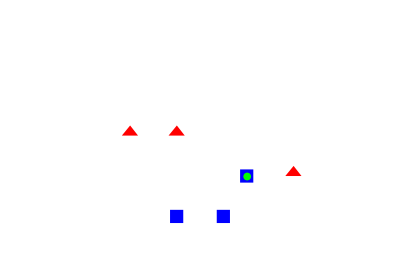

```mathematica
showGame@bm
```

```mathematica
bm2 = getBestMove[bm];
```

```mathematica
op = BlankSequence[];
turn = bm[[4]]
```

β

```mathematica
{homePlayers, awayPlayers} = {bm[[1]], bm[[2]]};
```

```mathematica
ballLoc = bm[[3]]
```

{9/2,√3}

```mathematica
{attackingTeam, attackerTurn} = If[MemberQ[homePlayers, ballLoc], {"home", "α"},{"away", "β"}]
```

{home,α}

```mathematica
{players, oppPlayers}=  If[turn == "α", {bm[[1]], bm[[2]]},{bm[[2]], bm[[1]]}] ;
```

```mathematica
pos = MemberQ[players, ballLoc]
```

False

```mathematica
{attackers, defenders} = If[pos, {players, oppPlayers}, {oppPlayers, players}];
```

```mathematica
currentGameState = {homePlayers, awayPlayers , ballLoc, turn, initialGuardCount};
```

```mathematica
showGame@currentGameState
```

-Graphics-

```mathematica
pg = FirstPosition[attackers, ballLoc][[1]];
```

```mathematica
attackerTurn
```

α

```mathematica
amoves = getAttackerMoves[attackers,ballLoc, attackerTurn, pg];
```

```mathematica
Length@amoves
```

240

```mathematica
amovesFiltered = filterMoves[amoves,True, ballLoc, pg];
```

```mathematica
Length@amovesFiltered
```

6

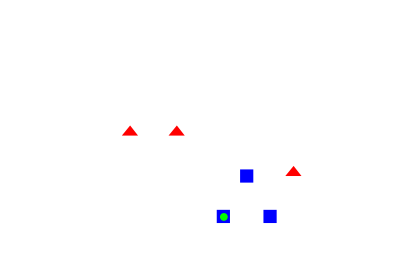
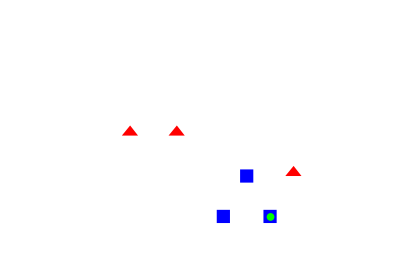
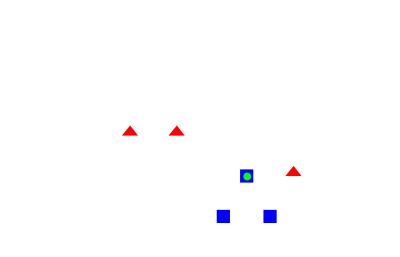
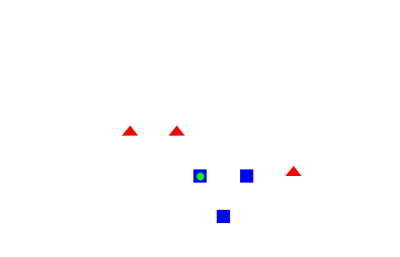
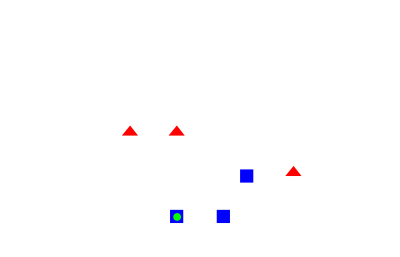
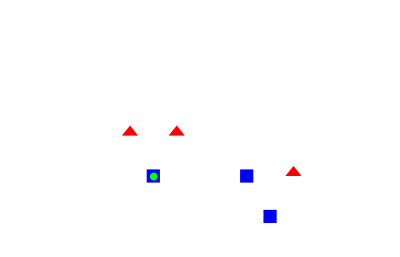

```mathematica
overlayAttackingMove[currentGameState, #]&/@ amovesFiltered
```

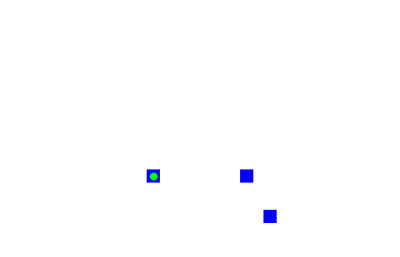
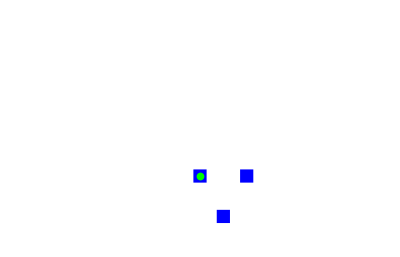
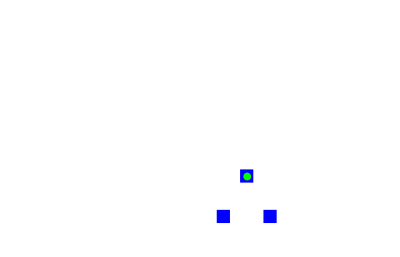
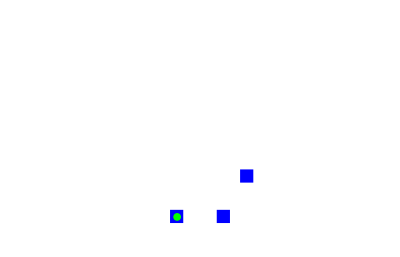
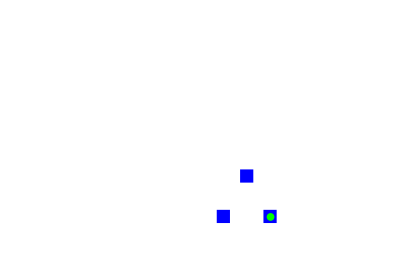

```mathematica
bestAttackingMoves=  TakeLargestBy[amovesFiltered, evaluateAttackingState[#,defenders, attackingTeam]&, UpTo[5]];
 showAttackingMove[#, "home"]&/@ bestAttackingMoves
```

```mathematica
dmoves= getDefenderMoves[defenders];
```

```mathematica
bestDefensiveMoves = getBestDefensiveMoves[defenders, bestAttackingMoves[[All, 3]], 3]
```

{{{3,1/10+(3 √3)/2},{5/2,1/10+2 √3},{9/2,1/10+√3}},{{3,1/10+(3 √3)/2},{7/2,1/10+2 √3},{9/2,1/10+√3}},{{3,1/10+(3 √3)/2},{4,1/10+(3 √3)/2},{9/2,1/10+√3}}}

```mathematica
overlayDefendingMove//Clear
```

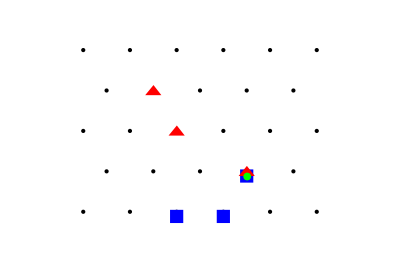
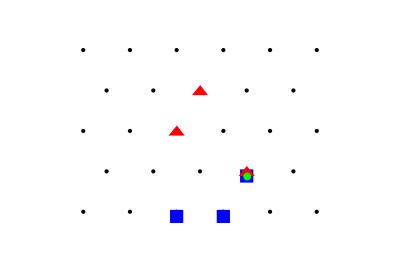
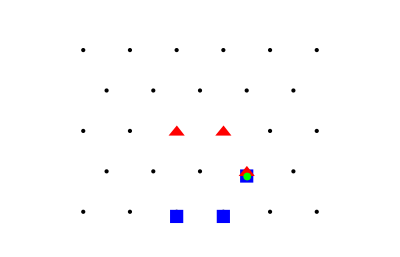

```mathematica
overlayDefendingMove[currentGameState, #, points->awayLocs]&/@ bestDefensiveMoves
```

```mathematica
bm2= If[pos, getAttackerGameState[First@bestAttackingMoves,currentGameState],
bestDefensiveMoves = getBestDefensiveMoves[defenders, bestAttackingMoves[[All, 3]], 3]; 
getDefenderGameState[First@bestDefensiveMoves, currentGameState]]
```

{{{3,(√3)/2},{4,(√3)/2},{9/2,√3}},{{3/2,1/10+2 √3},{7/2,1/10+√3},{6,1/10+(3 √3)/2}},{9/2,√3},α,0}

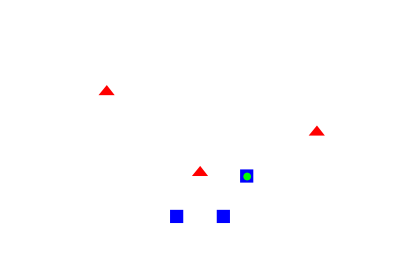

```mathematica
showGame@bm2
```

#### Testing Turnover

```mathematica
ClearAll@getBestMove
```

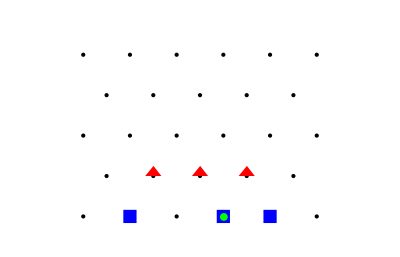

```mathematica
showGame[initialGameState,points->homeLocs]
```

```mathematica
to = ReplacePart[initialGameState, {{1, 1}-> homeLocs[[8]],3->homeLocs[[8]] }]
```

{{{5/2,√3},{4,(√3)/2},{5,(√3)/2}},{{5/2,1/10+√3},{7/2,1/10+√3},{9/2,1/10+√3}},{5/2,√3},α,0}

```mathematica
toMove = Append[to[[2]],to[[3]]]
```

{{5/2,1/10+√3},{7/2,1/10+√3},{9/2,1/10+√3},{5/2,√3}}

```mathematica
N@evaluateAttackingState[toMove, to[[2]], "home"]
```

-1.73205

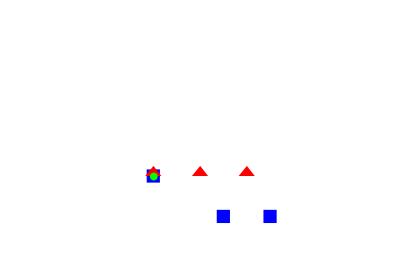

```mathematica
showGame@to
```

#### DFS

```mathematica
getLegalGamesDFS[initialGames_]:= Flatten[Map[getLegalGames[#, shorten->True]&, initialGames], 1]
```

```mathematica
nestGraphWithoutTheGraph[f_,x_,0]:=Null
nestGraphWithoutTheGraph[f_,x_,n_]:=Scan[nestGraphWithoutTheGraph[f,#,n-1]&,f[x]]
```

```mathematica
n = NestList[getLegalGamesDFS, {initialGameState}, 2]
```

#### Gameplay

To do: fix

```mathematica
moves =  NestList[getRandomBestGame[#, 5]&, initialGameState, 10];
```

```mathematica
moves = NestWhileList[getRandomBestGame[#, 5]&, initialGameState, !turnoverQ[#]&];
```

```mathematica
showPlay//ClearAll
```

```mathematica
showPlay[moves, points->allLocs]
```

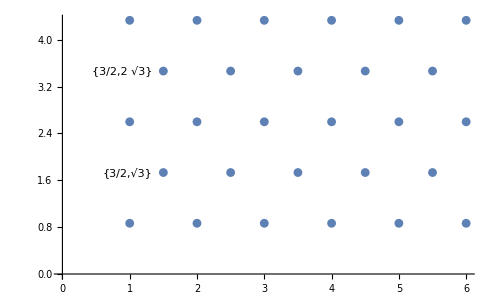

```mathematica
ListPlot[Labeled[#, #]&/@ homeLocs]
```

#### Gameplay V2

```mathematica
gs = NestList[getBestMove, initialGameState, 40];
```

```mathematica
graphics = showPlay[gs];
```

```mathematica
showPlay[gs]
```

```mathematica
FrameListVideo[graphics, FrameRate->15]
```

#### Court V2

```mathematica
courtWidth = 5;
courtLength =4;
directions = NestList[#+60Degree&, 0Degree, 5];
bottomLeftPoint = {1, 1};
background = Rectangle[bottomLeftPoint - {1, 1/2}, {courtWidth+2, courtLength+1}];
p = getPoint[bottomLeftPoint, 60Degree, 1]; 
{shortRowOffset, rowDiff} =p - bottomLeftPoint;
longRows = Table[NestList[getPoint[#, 0, 1]&, 
{bottomLeftPoint[[1]], (i - bottomLeftPoint[[2]]+ 1)*rowDiff},
 courtWidth], 
{i, bottomLeftPoint[[2]], courtLength+1, 2}];
shortRows = Table[NestList[getPoint[#, 0, 1]&, {p[[1]], (i - p[[2]]+2)*rowDiff}, courtWidth-1], {i, p[[2]], courtLength+1, 2}];
homeLocs = Flatten[Riffle[longRows, shortRows], 1];
homeAwayDistance = 1/10;
awayLocs = getAwayPoints[homeLocs, homeAwayDistance];
homeEndZoneY = homeLocs[[-1, 2]];
awayEndZoneY = awayLocs[[1, 2]];
allLocs = Join[homeLocs, awayLocs]; gamePoly = BoundingRegion[allLocs, "MinConvexPolygon"];
gamePoly = BoundingRegion[allLocs, "MinConvexPolygon"];
```

#### Object Parameters

```mathematica
playerSize = 1/5;
ballSize = 1/12;
playerSpeed = 1;
ballSpeed= 2;
stealDifficulty = 1;
```

#### Initialization

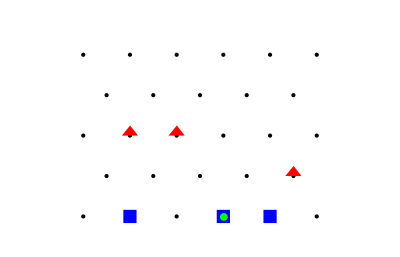

```mathematica
homePlayers = homeLocs[[{2, 4, 5}]];
awayPlayers = awayLocs[[{13, 14, 11}]];
allPlayers = Join[homePlayers, awayPlayers];
turn = "α";
dribbler = 2;
ballLoc = getPlayerLoc["home", dribbler];
initialGuardCount = 0;
initialGameState = {homePlayers, awayPlayers, ballLoc, turn, initialGuardCount};
showGame[initialGameState, points->homeLocs]
```

```mathematica
N@p[[1]]
```

1.5

### Discrete 2D General Functionality

### Discrete 2D Graphics Exploration

```mathematica
getRecPoints[point_, size_]:={getPoint[point, 225Degree, size], getPoint[point, 45Degree, size]}
getTriPoints[point_, size_]:=
{getPoint[point, 88Degree, size - 1/12],getPoint[point, 210 Degree, size], getPoint[point, 330Degree, size ]}
```

```mathematica
getBallLocation[team_,possessor_]:= Module[{shape},
shape=  
If[team == "home", 
Rectangle@@getRecPoints[homePlayers[[possessor]], playerSize],
Polygon[getTriPoints[awayPlayers[[possessor]], playerSize]]];
RegionCentroid[shape]
]
showGame[{homePlayers_, awayPlayers_ , ballLoc_, turn_}]:=Module[{hpRecs, apTris, allShapes, dribbler,ball},
hpRecs = Rectangle@@getRecPoints[#, playerSize]&/@ homePlayers;apTris = N/@Polygon@getTriPoints[#,playerSize]&/@ awayPlayers;
ball = Disk[ballLoc, ballSize];
Graphics[{FaceForm@Blue, hpRecs,FaceForm@Red ,apTris, Green, ball}, ImageSize->{200, 200}]
]
```

```mathematica
getPlayerLoc[team_, i_]:= If[team == "home", homePlayers[[i]], awayPlayers[[i]]]
```

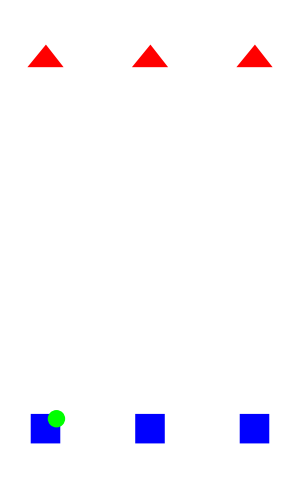

```mathematica
showGame[gameStates[[1]]]
```

```mathematica
MissingQ[Missing["NotFound"]]
```

True

#### Visualize game

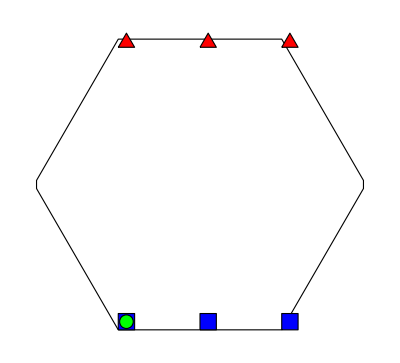

```mathematica
Module[{ courtLength, ballSize, playerSize, homeLocs, awayLocs, allLocs,hplayers, aplayers,allPlayers, gamePoly}, 
courtLength =2;ballSize = 1/12;playerSize = 1/5;
homeLocs = getHomePoints[courtLength];
awayLocs = getAwayPoints[homeLocs];
allLocs = Join[homeLocs, awayLocs];
hplayers = homeLocs[[{8, 13, 17}]];
aplayers = homeLocs[[{3, 7, 12}]];
allPlayers = Join[hplayers, aplayers];
gamePoly = BoundingRegion[allLocs, "MinConvexPolygon"];
showGame[gamePoly, hplayers, aplayers, getBallLocation["home", 1]]
]
```

#### Piece Movements

```mathematica
getMovesBounded[currentPoint_, speed_:1]:=Module[{allPoints},
allPoints = Map[getPoint[currentPoint, #, speed]&, directions];
Select[allPoints, RegionMember[gamePoly, #]&]
]
```

```mathematica
turn  = "α";
dribbler = 1;
ballLoc = getPlayerLoc["home", 1];
gameState = {homePlayers, awayPlayers, ballLoc, turn};
ballSpeed = 2;
```

Part::partd: Part specification homePlayers⟦1⟧ is longer than depth of object.

### Discrete 2D Graph Version 1

```mathematica
getDefenderGraph[]:=
Module[{attackerEdges, attackerLines, defenderVertices},
attackerEdges = EdgeList[getAttackerGraph[]];
attackerLines = edgeToLine/@ attackerEdges;
defenderVertices = Midpoint[#]&/@ attackerLines;
NearestNeighborGraph[defenderVertices, VertexCoordinates->defenderVertices]]
```

```mathematica
getAttackerGraph[]:=
Module[{bottomLeft, radius, angle, left, bottomRight, midLeft, topLeft, attackerVertices, attackerGraph},
bottomLeft={0, 0};radius=1;angle=60 Degree;bottomRight = {1, 0};
left = getPoint[bottomLeft,120Degree,radius];
midLeft  = getPoint[left, angle, radius];
topLeft =  getPoint[midLeft, 120Degree, radius];
attackerVertices = 
Join[
NestList[getPoint[#, angle, radius]&, left, 3],
NestList[getPoint[#, angle, radius]&, bottomLeft, 3],
NestList[getPoint[#, angle, radius]&, bottomRight, 1],
NestList[getPoint[#, angle, radius]&, topLeft, 1]
];
attackerGraph = NearestNeighborGraph[attackerVertices, {}, VertexCoordinates->attackerVertices]
]
```

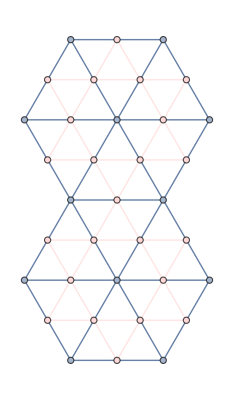

```mathematica
Module[{ag, dg},
ag = getAttackerGraph[];
dg = getDefenderGraph[];
combineTeamGraphs[ag, dg]
]
```

### Discrete 2D Graph Version 2

Here I’m going to have the attackers and defenders move on the same node pairs.

#### Game Construction

```mathematica
getAwayGraph[homeGraph_, homeAwayDistance_:0.1]:=
Module[{awayVertices},
awayVertices = getAwayPoints[VertexList@homeGraph];
NearestNeighborGraph[awayVertices, VertexCoordinates->awayVertices]]
```

```mathematica
getHexRow[startPoint_, rowLength_]:= NestList[getPoint[#, 60Degree, 1]&, startPoint, rowLength]
```

```mathematica
getGameGraphHex[length_]:=Module[{homeVertices, ag, dg},
homeVertices = getHomePoints[length];ag = NearestNeighborGraph[homeVertices, {}, VertexCoordinates->homeVertices];dg = getAwayGraph[ag];combineTeamGraphs[ag, dg]]
```

```mathematica
combineTeamGraphs[homeGraph_, awayGraph_]:= 
Module[{awayEdges, awayVertices, homeEdges, homeVertices },
awayEdges = EdgeList[awayGraph];
awayVertices = VertexList@awayGraph;
homeEdges = EdgeList@homeGraph;
homeVertices = VertexList@homeGraph;
Graph[Join[homeVertices,  (Style[#, LightRed]&/@awayVertices)], Join[homeEdges, (Style[#, LightRed]&/@awayEdges)], VertexCoordinates->Join[homeVertices, awayVertices]]
]
```

Note: as you increase speed you will want to allow for change of directions where this function will not work. Need to do some sort of depth first search thing

```mathematica
showMoves[currentPoint_, speed_:1]:=Module[{edgesStyled},
legalMoves = getMovesBounded[currentPoint, speed];
edgesStyled = Style[UndirectedEdge[currentPoint, #],Thick, Red]&/@ legalMoves;
 HighlightGraph[gameGraph, edgesStyled]]
```

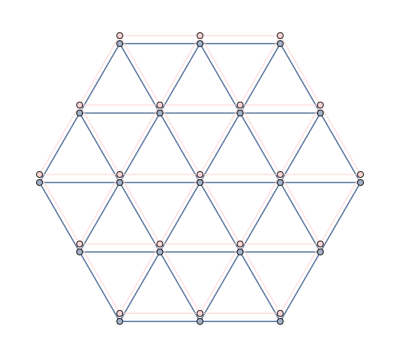

```mathematica
gameGraph = getGameGraphHex[2]
```

#### Visualize Piece Movement

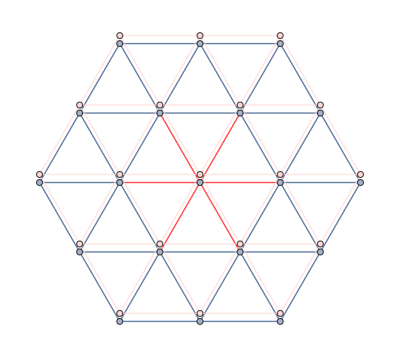

```mathematica
directions = NestList[#+60Degree&, 0Degree, 5];
playerSpeed = 1;
currentPoint = {2, 0};
showMoves[currentPoint, playerSpeed]
```

## Styling

```mathematica
getColorInputForm[color_]:=InputForm@RGBColor@color
```

```mathematica
ColorSetter[Dynamic[offensiveColor]]
```

$CellContext`offensiveColor

```mathematica
getColorInputForm[offensiveColor]
```

RGBColor[0.0861371786068513, 0.27838559548332953, 0.8631418326085298]

```mathematica
attackerColor =RGBColor[0.0861371786068513,0.27838559548332953,0.8631418326085298]
```

RGBColor[0.0861371786068513, 0.27838559548332953, 0.8631418326085298]

```mathematica
ColorSetter[Dynamic[defensiveColor]]
```

$CellContext`defensiveColor

```mathematica
defenderColor =RGBColor[0.8807965209430075,0.,0.04405279621576257]
```

RGBColor[0.8807965209430075, 0., 0.04405279621576257]

```mathematica
ColorSetter[Dynamic[successColor]]
```

$CellContext`successColor

```mathematica
successColor = RGBColor[0.2174563210498207,0.6534676127260243,0.06826886396581978]
```

RGBColor[0.2174563210498207, 0.6534676127260243, 0.06826886396581978]

```mathematica
ColorSetter[Dynamic[neutralColor]]
```

$CellContext`neutralColor

```mathematica
getColorInputForm[neutralColor]
```

RGBColor[0.37752346074616616, 0.37750820172426947, 0.37750820172426947]

```mathematica
neutralColor = RGBColor[0.37752346074616616,0.37750820172426947,0.37750820172426947]
```

RGBColor[0.37752346074616616, 0.37750820172426947, 0.37750820172426947]

```mathematica
ColorSetter[Dynamic[coveredColor]]
```

$CellContext`coveredColor

```mathematica
coveredColor = RGBColor[0.4669565880827039,0.07298390173189899,0.5677576867322804]
```

RGBColor[0.4669565880827039, 0.07298390173189899, 0.5677576867322804]

RGBColor[0.4669565880827039, 0.07298390173189899, 0.5677576867322804]

## Scratchpad

```mathematica
testRules = {1->a, 2->b}
```

{1→a,2→b}

```mathematica
testRules/.Rule->List
```

{{1,a},{2,b}}

```mathematica
testRuleList = ReplaceAll[testRules, Rule->List]
```

{{1,a},{2,b}}

```mathematica
Replace[testRuleList, List->Rule, {1}]
```

testRuleList